```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
(*For extracting the argument of a function*)
finv[_[x__]]:=x
```

```mathematica
(*Recursion for generating the solution polynomials*)
g[-1,a_,b_]=(1/b);
g[0,a_,b_] = 1;
g[n_,a_,b_]:=(a+2*b)*g[n-1,a,b]-b^2*g[n-2,a,b];
```

```mathematica
(*Onset or SS*)
Y[n_,ntot_,AoL_,Y0_]:=g[ntot-n-1,AoL,1]*Y0/g[ntot-1,AoL,1]
```

```mathematica
(*Make a piecewise function to fit experimental data*)
YPW[AoL_,mpw_,ntotpw_,Y0pw_]:=Piecewise[Table[{Simplify[Y[npw,ntotpw,AoL,Y0pw]],mpw-1== npw},{npw,0,ntotpw-1}]]
```

```mathematica
(*Only include wings with stereocilium0 displacements and at least 5 stereocilia*)
Data=Import["/Users/dmelody/Dropbox/Stereocilia/AlexData/PaperData/peak_steady_sd_se_fullwings.csv"];
(*Each wing starts at stereocilium 0*)
wingindex=Flatten[Position[Data[[All,3]],0]];
(*Number of wings*)
Length[wingindex]
(*Total number of stereocilia*)
Length[Data[[All,2]]]-1
```

38

302

```mathematica
Data[[1,All]]
Data[[1,3]]
Data[[1,4]]
Data[[1,9]]
```

{wing_id,wing_id2,norm_position_id,peak_nm_y,peak_nm_y_n,peak_nm_y_sd,peak_nm_y_se,peak_nm_y_max,steady_nm_y,steady_nm_y_n,steady_nm_y_sd,steady_nm_y_se}

norm_position_id

peak_nm_y

steady_nm_y

```mathematica
(*Number of stereocilia with an overshoot excluding stereocilium0*)
Total[Flatten[Table[Table[If[Data[[n,4]]-Data[[n,9]]>0,1,0],{n,wingindex[[wingindexnum]]+1,If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],{wingindexnum,1,Length[wingindex]}]]]
(*Total number of stereocilia excluding stereocilium0*)
Length[Data[[All,2]]]-1-Length[wingindex]
(*Fraction of stereocilia with an overshoot*)
N[Total[Flatten[Table[Table[If[Data[[n,4]]-Data[[n,9]]>0,1,0],{n,wingindex[[wingindexnum]]+1,If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],{wingindexnum,1,Length[wingindex]}]]]/(Length[Data[[All,2]]]-1-Length[wingindex])]
```

209

264

0.791667

```mathematica
(*****************************************************************)
```

```mathematica
(*Exclude wings with a negative onset or steady-state because this indicates a damaged wing or a measurement artifact. 7 wings have negative onsets or ss. 38-7 = 31*)
Position[Table[Total[Table[If[Data[[n,4]]<0||Data[[n,9]]<0,1,0],{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]],{wingindexnum,1,Length[wingindex]}],_?(#>0&)]
Length[Position[Table[Total[Table[If[Data[[n,4]]<0||Data[[n,9]]<0,1,0],{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]],{wingindexnum,1,Length[wingindex]}],_?(#>0&)]]
```

{{2},{4},{5},{12},{19},{23},{38}}

7

```mathematica
(*7 wings have negative onsets or ss. 38-7 = 31*)
wingindexnum = 2;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 4;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 5;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 12;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 19;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 23;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
wingindexnum = 38;
{Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}],
Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}]}
```

{{{0,369.65},{1,148.421},{2,91.1},{3,58.8714},{4,50.3857},{5,38.4714},{6,19.2714},{7,11.7214},{8,9.8},{9,-1.07143}},{{0,598.25},{1,231.05},{2,123},{3,63.1},{4,43.6},{5,31.4},{6,19.4},{7,7.25},{8,7.8},{9,13.8}}}

{{{0,54.2929},{1,37.4714},{2,13.0643},{3,2.4},{4,-2.47143},{5,3.15},{6,-0.5}},{{0,53.55},{1,32.1},{2,11.05},{3,-0.2},{4,1.3},{5,2.45},{6,2.1}}}

{{{0,133.779},{1,61.5357},{2,50.6},{3,25.5143},{4,2.78571},{5,20.9357},{6,9.6},{7,28.1071}},{{0,117.35},{1,44.7},{2,29.9},{3,11.4},{4,-1.5},{5,14.25},{6,8.75},{7,11.6}}}

{{{0,83.3786},{1,72.3786},{2,38.9786},{3,33.4929},{4,17.8857},{5,10.4857},{6,8.28571},{7,-2.61429}},{{0,88},{1,75.45},{2,34.55},{3,19.05},{4,12.5},{5,2.7},{6,0.15},{7,-2.65}}}

{{{0,182.717},{1,111.667},{2,75.2667},{3,48.7667},{4,22.7167},{5,18.65},{6,1.76667},{7,7.55},{8,2.55},{9,-8.31667}},{{0,194.7},{1,112.95},{2,85.175},{3,46.075},{4,14.075},{5,17},{6,-0.15},{7,5.25},{8,1.475},{9,-10.6}}}

{{{0,57.8286},{1,33.6286},{2,22.0143},{3,11.5786},{4,5.42857},{5,7.62143},{6,0.0928571},{7,1.87857},{8,0.1},{9,4.72143}},{{0,61.8},{1,27.75},{2,16.15},{3,7.5},{4,3.5},{5,-1.1},{6,3},{7,1.9},{8,-2.05},{9,-2}}}

{{{0,161.15},{1,102.229},{2,76.45},{3,53.9},{4,34.0571},{5,20.5857},{6,13.5286},{7,10.1929},{8,6.77143}},{{0,172.05},{1,99.55},{2,48.75},{3,37.9},{4,8.95},{5,1.7},{6,-0.45},{7,-3.65},{8,-1.05}}}

```mathematica
(*****************************)
```

```mathematica
onsetList = Table[NaN,{n,1,Length[wingindex]}];
onsetnstereoList = Table[NaN,{n,1,Length[wingindex]}];onsetAoLList = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
onsetAoLPvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetY0List = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
onsetY0PvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetAdjRsqList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetExportTable=Table[{NaN,NaN,NaN,NaN,NaN,NaN},{n,1,Length[wingindex]}];(*Index of analyzed wings*)
analwingindex = 0;
onsetanal = Table[n,{n,1,31}];
ssanal = Table[n,{n,1,31}];
For[wingindexnum = 1, wingindexnum ≤ Length[wingindex],wingindexnum++,
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
If[Length[Select[onset[[All,2]],#<0&]]+Length[Select[ss[[All,2]],#<0&]]>0,Continue[],analwingindex = analwingindex+1;
onsetErr=Table[{Data[[n,3]],Data[[n,6]]/Sqrt[Data[[n,5]]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
ssErr=Table[{Data[[n,3]],Data[[n,11]]/Sqrt[Data[[n,10]]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
onsetanal[[analwingindex]]=Join[{analwingindex},{Table[{onset[[n,1]],Around[onset[[n,2]],onsetErr[[n,2]]]},{n,1,Length[onset]}]}];
ssanal[[analwingindex]]=Join[{analwingindex},{Table[{ss[[n,1]],Around[ss[[n,2]],ssErr[[n,2]]]},{n,1,Length[ss]}]}];]]
```

```mathematica
onsetList = Table[NaN,{n,1,Length[wingindex]}];
onsetnstereoList = Table[NaN,{n,1,Length[wingindex]}];onsetAoLList = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
onsetAoLPvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetY0List = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
onsetY0PvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetAdjRsqList = Table[{n,NaN},{n,1,Length[wingindex]}];
onsetExportTable=Table[{NaN,NaN,NaN,NaN,NaN,NaN},{n,1,Length[wingindex]}];
```

analwingindex = 1

wingindexnum = 1

S8731025_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.263558 | 0.028525 | 9.23953 | 0.000090762
Y0onset | 364.877 | 35.9341 | 10.1541 | 0.0000530807

AdjustedRSquared | 0.980438
AIC | 64.8256
BIC | 65.064
RSquared | 0.985328

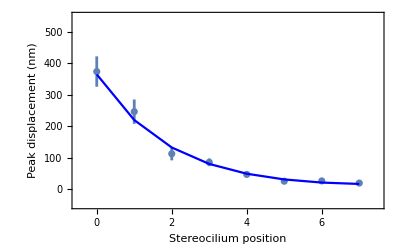

analwingindex = 2

wingindexnum = 3

S8731027_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.184873 | 0.0151669 | 12.1892 | 1.90278×10^-6
Y0onset | 403.539 | 32.1748 | 12.5421 | 1.52994×10^-6

AdjustedRSquared | 0.944559
AIC | 95.1203
BIC | 96.028
RSquared | 0.955647

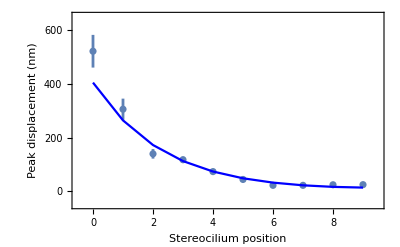

analwingindex = 3

wingindexnum = 6

S8731036_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.284436 | 0.00507923 | 55.9998 | 3.43469×10^-8
Y0onset | 364.917 | 1.45268 | 251.202 | 1.89719×10^-11

AdjustedRSquared | 0.995306
AIC | 255.531
BIC | 255.369
RSquared | 0.996647

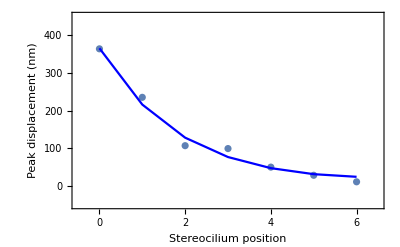

analwingindex = 4

wingindexnum = 7

S8731036_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.279249 | 0.00767818 | 36.3691 | 2.95889×10^-7
Y0onset | 179.263 | 1.56741 | 114.368 | 9.69208×10^-10

AdjustedRSquared | 0.988281
AIC | 166.548
BIC | 166.386
RSquared | 0.991629

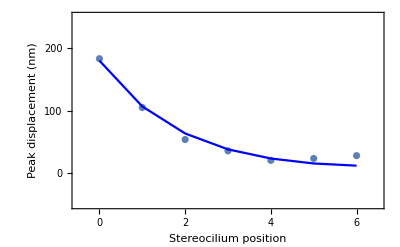

analwingindex = 5

wingindexnum = 8

S8731044_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.299858 | 0.00846557 | 35.4208 | 3.37529×10^-8
Y0onset | 219.025 | 1.84711 | 118.577 | 2.42556×10^-11

AdjustedRSquared | 0.992645
AIC | 142.243
BIC | 142.481
RSquared | 0.994484

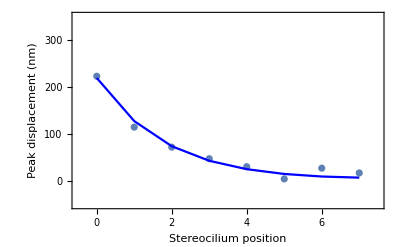

analwingindex = 6

wingindexnum = 9

S8731045_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.242363 | 0.00496274 | 48.8367 | 4.94269×10^-9
Y0onset | 259.479 | 1.0454 | 248.21 | 2.88587×10^-13

AdjustedRSquared | 0.997214
AIC | 181.284
BIC | 181.523
RSquared | 0.99791

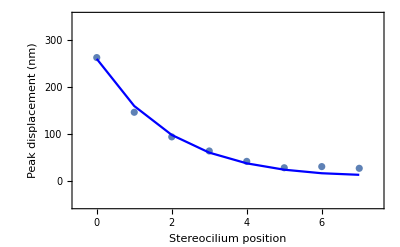

analwingindex = 7

wingindexnum = 10

S8731047_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.279735 | 0.00391101 | 71.5251 | 1.01182×10^-8
Y0onset | 444.78 | 4.00306 | 111.11 | 1.11985×10^-9

AdjustedRSquared | 0.970443
AIC | 506.133
BIC | 505.97
RSquared | 0.978888

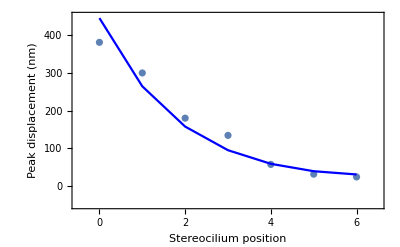

analwingindex = 8

wingindexnum = 11

S8731047_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.233129 | 0.00195691 | 119.131 | 7.90399×10^-10
Y0onset | 394.266 | 1.78402 | 220.999 | 3.59962×10^-11

AdjustedRSquared | 0.998458
AIC | 103.039
BIC | 102.877
RSquared | 0.998899

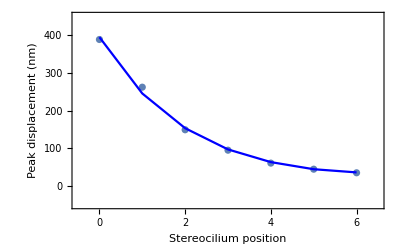

analwingindex = 9

wingindexnum = 13

S8802010_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.156145 | 0.0195441 | 7.98937 | 0.000091926
Y0onset | 67.0497 | 1.70487 | 39.3283 | 1.78952×10^-9

AdjustedRSquared | 0.991115
AIC | 56.4751
BIC | 57.0668
RSquared | 0.993089

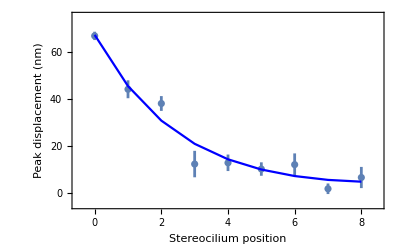

analwingindex = 10

wingindexnum = 14

S8802010_left_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.16321 | 0.0035823 | 45.56 | 7.4905×10^-9
Y0onset | 405.096 | 3.13007 | 129.421 | 1.43507×10^-11

AdjustedRSquared | 0.968817
AIC | 651.945
BIC | 652.183
RSquared | 0.976612

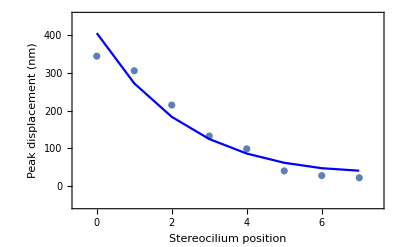

analwingindex = 11

wingindexnum = 15

S8802010_right_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.127102 | 0.0034558 | 36.7793 | 2.85479×10^-9
Y0onset | 325.11 | 3.89075 | 83.5599 | 9.25629×10^-12

AdjustedRSquared | 0.985262
AIC | 214.082
BIC | 214.674
RSquared | 0.988537

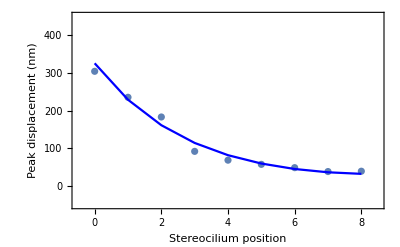

analwingindex = 12

wingindexnum = 16

S8802010_right_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.110505 | 0.00154834 | 71.3696 | 2.78823×10^-11
Y0onset | 642.04 | 4.78486 | 134.181 | 3.36824×10^-13

AdjustedRSquared | 0.990418
AIC | 347.032
BIC | 347.624
RSquared | 0.992547

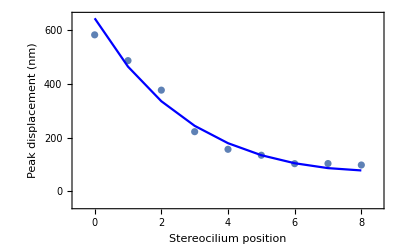

analwingindex = 13

wingindexnum = 17

S8802012_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.162855 | 0.00565485 | 28.7991 | 1.16094×10^-7
Y0onset | 101.526 | 1.28157 | 79.2194 | 2.72412×10^-10

AdjustedRSquared | 0.986658
AIC | 121.305
BIC | 121.544
RSquared | 0.989993

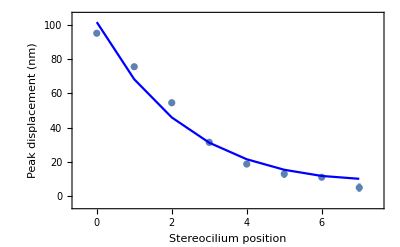

analwingindex = 14

wingindexnum = 18

S8802012_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.178796 | 0.0096899 | 18.4517 | 3.40416×10^-7
Y0onset | 74.1314 | 0.951961 | 77.8723 | 1.51543×10^-11

AdjustedRSquared | 0.984915
AIC | 116.883
BIC | 117.475
RSquared | 0.988267

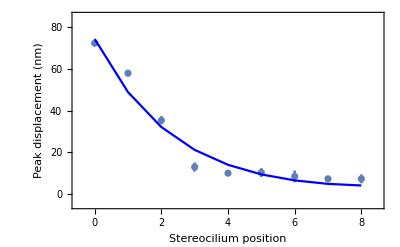

analwingindex = 15

wingindexnum = 20

S8804012_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.309909 | 0.00336088 | 92.2106 | 8.29252×10^-8
Y0onset | 409. | 1.17543 | 347.958 | 4.0928×10^-10

AdjustedRSquared | 0.996052
AIC | 392.652
BIC | 392.027
RSquared | 0.997368

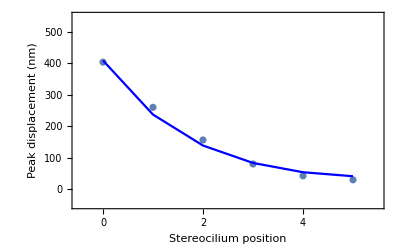

analwingindex = 16

wingindexnum = 21

S8804014_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.244084 | 0.00201593 | 121.078 | 1.24214×10^-6
Y0onset | 200.38 | 0.605936 | 330.696 | 6.09778×10^-8

AdjustedRSquared | 0.995102
AIC | 495.389
BIC | 494.217
RSquared | 0.997061

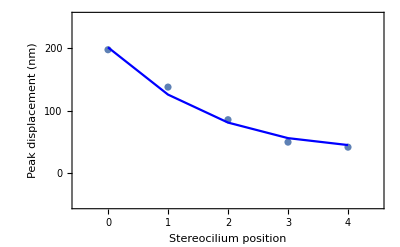

analwingindex = 17

wingindexnum = 22

S8804020_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.310177 | 0.00486022 | 63.8196 | 3.61098×10^-7
Y0onset | 566.882 | 2.41682 | 234.557 | 1.982×10^-9

AdjustedRSquared | 0.998039
AIC | 152.575
BIC | 151.95
RSquared | 0.998693

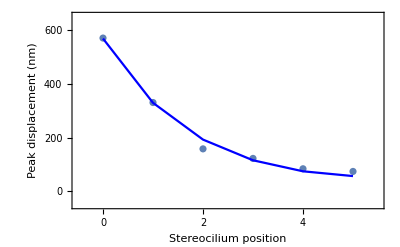

analwingindex = 18

wingindexnum = 24

S8807001_right_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.201695 | 0.00690555 | 29.2077 | 2.04475×10^-9
Y0onset | 232.251 | 2.37952 | 97.6038 | 1.35572×10^-13

AdjustedRSquared | 0.984613
AIC | 197.191
BIC | 198.099
RSquared | 0.987691

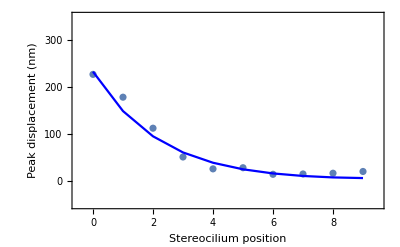

analwingindex = 19

wingindexnum = 25

S8807001_right_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.179807 | 0.00317212 | 56.6834 | 1.04156×10^-11
Y0onset | 447.833 | 5.53093 | 80.9688 | 6.03628×10^-13

AdjustedRSquared | 0.973665
AIC | 483.505
BIC | 484.412
RSquared | 0.978932

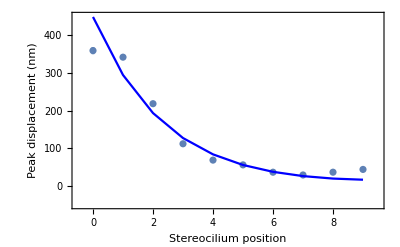

analwingindex = 20

wingindexnum = 26

S8807003_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.208526 | 0.00275186 | 75.7766 | 1.83393×10^-11
Y0onset | 302.342 | 1.96713 | 153.697 | 1.30232×10^-13

AdjustedRSquared | 0.9952
AIC | 274.789
BIC | 275.381
RSquared | 0.996267

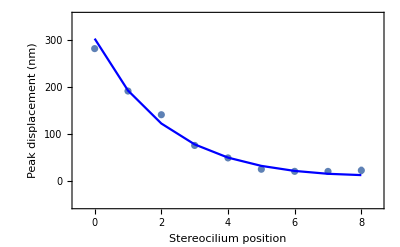

analwingindex = 21

wingindexnum = 27

S8807004_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.207544 | 0.00204634 | 101.422 | 9.97595×10^-14
Y0onset | 281.972 | 0.83393 | 338.124 | 6.55393×10^-18

AdjustedRSquared | 0.996726
AIC | 895.519
BIC | 896.427
RSquared | 0.997381

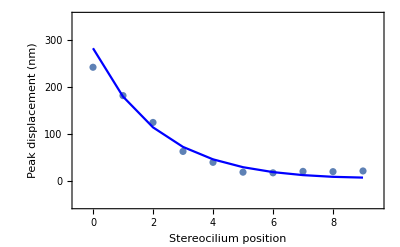

analwingindex = 22

wingindexnum = 28

S8807018_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.391498 | 0.0102408 | 38.2293 | 2.18043×10^-9
Y0onset | 223.285 | 2.14747 | 103.976 | 2.00615×10^-12

AdjustedRSquared | 0.996254
AIC | 84.0283
BIC | 84.62
RSquared | 0.997086

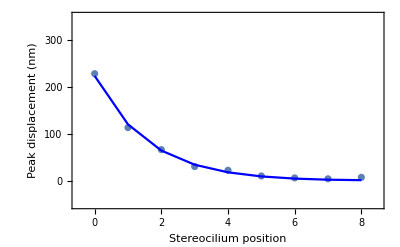

analwingindex = 23

wingindexnum = 29

S8808003_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.17132 | 0.00288044 | 59.4771 | 1.518×10^-9
Y0onset | 290.961 | 1.95342 | 148.949 | 6.17681×10^-12

AdjustedRSquared | 0.997645
AIC | 113.717
BIC | 113.956
RSquared | 0.998234

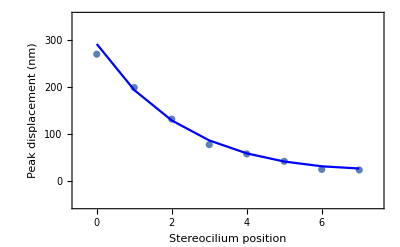

analwingindex = 24

wingindexnum = 30

S8809001_left_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.371074 | 0.0180049 | 20.6096 | 0.0000327405
Y0onset | 210.673 | 2.3045 | 91.4182 | 8.5837×10^-8

AdjustedRSquared | 0.975451
AIC | 243.785
BIC | 243.16
RSquared | 0.983634

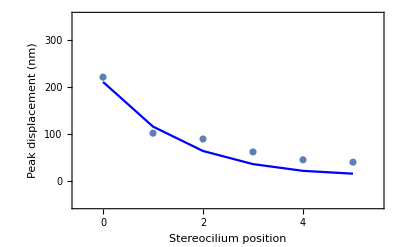

analwingindex = 25

wingindexnum = 31

S8809001_left_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.258737 | 0.00545807 | 47.4046 | 0.0000206688
Y0onset | 431.647 | 3.30858 | 130.463 | 9.92924×10^-7

AdjustedRSquared | 0.994222
AIC | 105.205
BIC | 104.033
RSquared | 0.996533

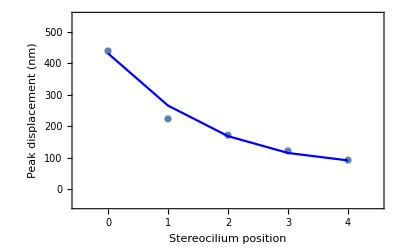

analwingindex = 26

wingindexnum = 32

S8809003_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.192735 | 0.00395807 | 48.6942 | 6.90171×10^-8
Y0onset | 200.683 | 1.49131 | 134.569 | 4.29858×10^-10

AdjustedRSquared | 0.967583
AIC | 641.286
BIC | 641.124
RSquared | 0.976845

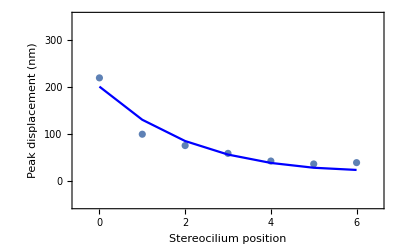

analwingindex = 27

wingindexnum = 33

S8809009_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.174456 | 0.0140221 | 12.4415 | 0.0000594759
Y0onset | 48.8343 | 1.30129 | 37.5275 | 2.5308×10^-7

AdjustedRSquared | 0.987909
AIC | 42.1609
BIC | 41.9986
RSquared | 0.991363

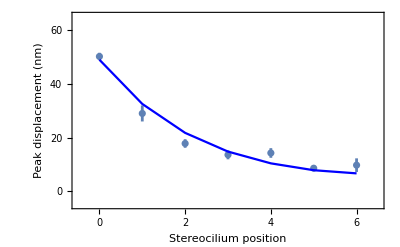

analwingindex = 28

wingindexnum = 34

S8809011_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.231913 | 0.032071 | 7.23125 | 0.000789093
Y0onset | 43.6601 | 1.98361 | 22.0105 | 3.59419×10^-6

AdjustedRSquared | 0.952635
AIC | 69.5074
BIC | 69.3451
RSquared | 0.966168

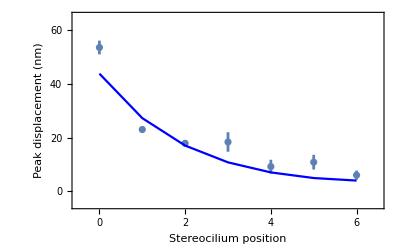

analwingindex = 29

wingindexnum = 35

S8811007_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.221795 | 0.00227751 | 97.3849 | 2.16449×10^-9
Y0onset | 209.467 | 0.133192 | 1572.67 | 1.97296×10^-15

AdjustedRSquared | 0.999442
AIC | 1012.63
BIC | 1012.46
RSquared | 0.999601

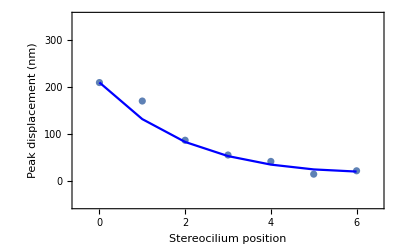

analwingindex = 30

wingindexnum = 36

S8811009_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.184474 | 0.00511568 | 36.0604 | 3.53024×10^-6
Y0onset | 106.466 | 1.1629 | 91.5526 | 8.53341×10^-8

AdjustedRSquared | 0.985373
AIC | 148.754
BIC | 148.129
RSquared | 0.990249

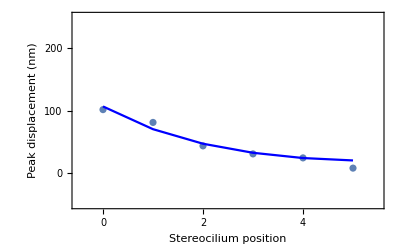

analwingindex = 31

wingindexnum = 37

S8811019_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.113523 | 0.001125 | 100.91 | 6.38322×10^-11
Y0onset | 144.43 | 0.632326 | 228.411 | 4.75196×10^-13

AdjustedRSquared | 0.997015
AIC | 288.119
BIC | 288.357
RSquared | 0.997761

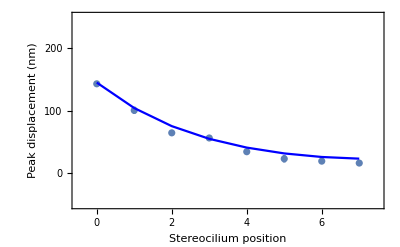

```mathematica
(*Fit wings with all positive onsets and ss*)
(*Index of analyzed wings*)
analwingindex = 0;
(*Fit weights are 1/SE^2 and there is a different number of points in each measurement window*)
For[wingindexnum = 1, wingindexnum ≤ Length[wingindex],wingindexnum++,
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
If[Length[Select[onset[[All,2]],#<0&]]+Length[Select[ss[[All,2]],#<0&]]>0,Continue[],analwingindex = analwingindex+1;Print["analwingindex = ",analwingindex];
Print["wingindexnum = ",wingindexnum];
onsetErr=Table[{Data[[n,3]],Data[[n,6]]/Sqrt[Data[[n,5]]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
onsetList[[wingindexnum]]=Join[{wingindexnum},{Table[{onset[[n,1]],Around[onset[[n,2]],onsetErr[[n,2]]]},{n,1,Length[onset]}]}];
nstereo=Last[onset[[All,1]]]+1;
fit=NonlinearModelFit[Table[onset[[n,2]],{n,1,Length[onset]}],{YPW[AoL,m,nstereo,Y0onset]},{AoL,{Y0onset,onset[[1,2]]}},m,Weights->Table[1/onsetErr[[n,2]]^2,{n,1,Length[onset]}],VarianceEstimatorFunction->(1&)];
onsetnstereoList[[wingindexnum]]=nstereo;
onsetAoLList[[wingindexnum,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
onsetAoLList[[wingindexnum,2]]=Evaluate[fit["ParameterErrors"][[1]]];
onsetAoLPvalList[[wingindexnum,2]]=Evaluate[fit["ParameterTable"][[1,1,2,5]]];
onsetY0List[[wingindexnum,1,2]]=Evaluate[Y0onset/.fit["BestFitParameters"][[2]]];
onsetY0List[[wingindexnum,2]]=Evaluate[fit["ParameterErrors"][[2]]];
onsetY0PvalList[[wingindexnum,2]]=Evaluate[fit["ParameterTable"][[1,1,3,5]]];
onsetAdjRsqList[[wingindexnum,2]]=Evaluate[fit["AdjustedRSquared"]];
onsetExportTable[[wingindexnum,1]]=Data[[wingindex[[wingindexnum]],1]];
onsetExportTable[[wingindexnum,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
onsetExportTable[[wingindexnum,3]]=Evaluate[fit["ParameterErrors"][[1]]];
onsetExportTable[[wingindexnum,4]]=Evaluate[Y0onset/.fit["BestFitParameters"][[2]]];
onsetExportTable[[wingindexnum,5]]=Evaluate[fit["ParameterErrors"][[2]]];
onsetExportTable[[wingindexnum,6]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum]],2]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = nstereo-1;
Ymin=0;
deltaY = 10^(MantissaExponent[onsetList[[wingindexnum,2,1,2]]["Value"]+onsetList[[wingindexnum,2,1,2]]["Uncertainty"]][[2]]-1);Ymax =Ceiling[onsetList[[wingindexnum,2,1,2]]["Value"]+onsetList[[wingindexnum,2,1,2]]["Uncertainty"],deltaY];
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Print[Show[ListPlot[onsetList[[wingindexnum,2]],PlotRange->{{-0.5,Xmax+0.5},{-deltaY/2,Ymax+deltaY/2}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Peak displacement (nm)"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],ListPlot[Table[{onset[[n,1]],YPW[onsetAoLList[[wingindexnum,1,2]],n,nstereo,onsetY0List[[wingindexnum,1,2]]]},{n,1,Length[onset]}],PlotStyle->Blue,Joined->True]]]]]
```

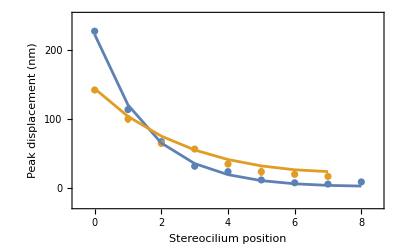

0.391498

0.113523

223.285

144.43

```mathematica
(*Example wings*)
wingindexnum1 = 28;
wingindexnum2 = 37;
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Max[Length[onsetList[[wingindexnum1,2]]],Length[onsetList[[wingindexnum2,2]]]]-1;
Ymin=0;
deltaY = 10^(MantissaExponent[Max[onsetList[[wingindexnum1,2,1,2]]["Value"]+onsetList[[wingindexnum1,2,1,2]]["Uncertainty"],onsetList[[wingindexnum2,2,1,2]]["Value"]+onsetList[[wingindexnum2,2,1,2]]["Uncertainty"]]][[2]]-1);Ymax =Ceiling[Max[onsetList[[wingindexnum1,2,1,2]]["Value"]+onsetList[[wingindexnum1,2,1,2]]["Uncertainty"],onsetList[[wingindexnum2,2,1,2]]["Value"]+onsetList[[wingindexnum2,2,1,2]]["Uncertainty"]],deltaY];
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Print[Show[ListPlot[{onsetList[[wingindexnum1,2]],onsetList[[wingindexnum2,2]]},PlotRange->{{-0.5,Xmax+0.5},{-deltaY/4,Ymax-deltaY/2}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Peak displacement (nm)"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],ListPlot[{Table[{onsetList[[wingindexnum1,2,n,1]],YPW[onsetAoLList[[wingindexnum1,1,2]],n,Length[onsetList[[wingindexnum1,2]]],onsetY0List[[wingindexnum1,1,2]]]},{n,1,Length[onsetList[[wingindexnum1,2]]]}],Table[{onsetList[[wingindexnum2,2,n,1]],YPW[onsetAoLList[[wingindexnum2,1,2]],n,Length[onsetList[[wingindexnum2,2]]],onsetY0List[[wingindexnum2,1,2]]]},{n,1,Length[onsetList[[wingindexnum2,2]]]}]},PlotStyle->Thickness[Linewidth],Joined->True]]]
onsetAoLList[[wingindexnum1,1,2]]
onsetAoLList[[wingindexnum2,1,2]]
onsetY0List[[wingindexnum1,1,2]]
onsetY0List[[wingindexnum2,1,2]]
```

```mathematica
(*****************Exported Data******************)
```

```mathematica
Data[[wingindex[[wingindexnum1]],1]]
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
onsetErr=Table[{Data[[n,3]],Data[[n,6]]/Sqrt[Data[[n,5]]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
nstereo=Last[onset[[All,1]]]+1;
fit=NonlinearModelFit[Table[onset[[n,2]],{n,1,Length[onset]}],{YPW[AoL,m,nstereo,Y0onset]},{AoL,{Y0onset,onset[[1,2]]}},m,Weights->Table[1/onsetErr[[n,2]]^2,{n,1,Length[onset]}],VarianceEstimatorFunction->(1&)];
onsetAoLList[[wingindexnum1,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
onsetAoLList[[wingindexnum1,2]]=Evaluate[fit["ParameterErrors"][[1]]];
onsetY0List[[wingindexnum1,1,2]]=Evaluate[Y0onset/.fit["BestFitParameters"][[2]]];
onsetY0List[[wingindexnum1,2]]=Evaluate[fit["ParameterErrors"][[2]]];
onsetAdjRsqList[[wingindexnum1,2]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum1]],1]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

S8807018_1_right

S8807018_1_right

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.391498 | 0.0102408 | 38.2293 | 2.18043×10^-9
Y0onset | 223.285 | 2.14747 | 103.976 | 2.00615×10^-12

AdjustedRSquared | 0.996254
AIC | 84.0283
BIC | 84.62
RSquared | 0.997086

```mathematica
Data[[wingindex[[wingindexnum2]],1]]
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
onsetErr=Table[{Data[[n,3]],Data[[n,6]]/Sqrt[Data[[n,5]]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
nstereo=Last[onset[[All,1]]]+1;
fit=NonlinearModelFit[Table[onset[[n,2]],{n,1,Length[onset]}],{YPW[AoL,m,nstereo,Y0onset]},{AoL,{Y0onset,onset[[1,2]]}},m,Weights->Table[1/onsetErr[[n,2]]^2,{n,1,Length[onset]}],VarianceEstimatorFunction->(1&)];
onsetAoLList[[wingindexnum2,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
onsetAoLList[[wingindexnum2,2]]=Evaluate[fit["ParameterErrors"][[1]]];
onsetY0List[[wingindexnum2,1,2]]=Evaluate[Y0onset/.fit["BestFitParameters"][[2]]];
onsetY0List[[wingindexnum2,2]]=Evaluate[fit["ParameterErrors"][[2]]];
onsetAdjRsqList[[wingindexnum2,2]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum2]],1]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

S8811019_1_left

S8811019_1_left

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.113523 | 0.001125 | 100.91 | 6.38322×10^-11
Y0onset | 144.43 | 0.632326 | 228.411 | 4.75196×10^-13

AdjustedRSquared | 0.997015
AIC | 288.119
BIC | 288.357
RSquared | 0.997761

```mathematica
(*Remove NaN entries*)
baddata[entry_]:=MatchQ[entry,{{_?NumberQ,NaN},NaN}];
onsetnstereoListrenum=DeleteCases[onsetnstereoList,NaN];
onsetAoLListtemp=DeleteCases[onsetAoLList,_?baddata];
onsetAoLListrenum=Table[{{n,onsetAoLListtemp[[n,1,2]]},onsetAoLListtemp[[n,2]]},{n,1,Length[onsetAoLListtemp]}];
baddata2[entry_]:=MatchQ[entry,{_?NumberQ,NaN}];
onsetAdjRsqListtemp=DeleteCases[onsetAdjRsqList,_?baddata2];
onsetAdjRsqListrenum=Table[{{n,onsetAdjRsqListtemp[[n,2]]}},{n,1,Length[onsetAdjRsqListtemp]}];
```

```mathematica
(*Minimum and maximum ratios*)
Min[onsetAoLListrenum[[All,1,2]]]
Max[onsetAoLListrenum[[All,1,2]]]
```

0.110505

0.391498

```mathematica
MedianOnsetAoL = Quantile[onsetAoLListrenum[[All,1,2]],0.5]
LowerQuantileOnsetAoL = Quantile[onsetAoLListrenum[[All,1,2]],0.25]
UpperQuantileOnsetAoL = Quantile[onsetAoLListrenum[[All,1,2]],0.75]
```

0.208526

0.174456

0.279249

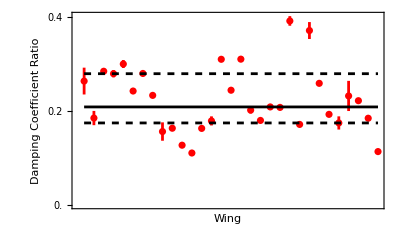

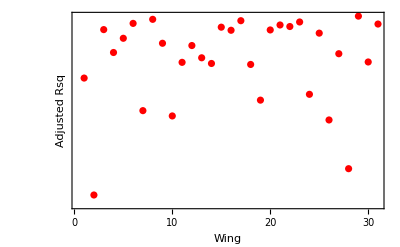

```mathematica
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Length[onsetAoLListrenum];
Ymin=0;Ymax =1;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,5}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,0.1}];
Show[ListPlot[Table[{onsetAoLListrenum[[n,1,1]],Around[onsetAoLListrenum[[n,1,2]],onsetAoLListrenum[[n,2]]]},{n,1,Length[onsetAoLListrenum]}],PlotRange->All,PlotStyle->{Thickness[Linewidth],Red},IntervalMarkersStyle->{Thickness[Linewidth],Red},Frame->{{True,False},{True,False}},FrameTicks->{None,YTicks},FrameLabel->{"Wing","Damping Coefficient Ratio"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[{MedianOnsetAoL,LowerQuantileOnsetAoL,UpperQuantileOnsetAoL},{n,1,Length[onsetAoLListrenum]},PlotStyle->{{Thickness[Linewidth],Black},{Thickness[Linewidth],Black,Dashed},{Thickness[Linewidth],Black,Dashed}}]]
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Length[onsetAoLListrenum];
Ymin=0;
Ymax =1;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,5}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,0.01}];
ListPlot[Table[{onsetAoLListrenum[[n,1,1]],onsetAdjRsqListrenum[[n,1,2]]},{n,1,Length[onsetAoLListrenum]}],PlotRange->All,PlotStyle->{Thickness[Linewidth],Red},IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Wing","Adjusted Rsq"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(*Minimum adjRsq*)
Min[onsetAdjRsqList[[All,2]]]
```

Min[0.944559,NaN]

```mathematica
(*Maximum P-value over all fit parameters*)
Max[{onsetAoLPvalList[[All,2]],onsetY0PvalList[[All,2]]}]
```

Max[0.000789093,NaN]

```mathematica
(*****************************)
```

```mathematica
ssList = Table[NaN,{n,1,Length[wingindex]}];
ssnstereoList = Table[NaN,{n,1,Length[wingindex]}];
ssAoLList = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
ssAoLPvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
ssY0List = Table[{{n,NaN},NaN},{n,1,Length[wingindex]}];
ssY0PvalList = Table[{n,NaN},{n,1,Length[wingindex]}];
ssAdjRsqList = Table[{n,NaN},{n,1,Length[wingindex]}];
ssExportTable=Table[{NaN,NaN,NaN,NaN,NaN,NaN},{n,1,Length[wingindex]}];
```

analwingindex = 1

wingindexnum = 1

S8731025_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.358482 | 0.00185639 | 193.106 | 1.30119×10^-12
Y0ss | 595.499 | 0.685954 | 868.133 | 1.57681×10^-16

AdjustedRSquared | 0.998791
AIC | 767.121
BIC | 767.359
RSquared | 0.999093

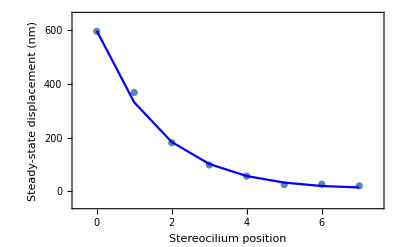

analwingindex = 2

wingindexnum = 3

S8731027_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.351645 | 0.00125866 | 279.379 | 3.01649×10^-17
Y0ss | 859.188 | 1.07141 | 801.923 | 6.54843×10^-21

AdjustedRSquared | 0.990046
AIC | 10386.8
BIC | 10387.7
RSquared | 0.992037

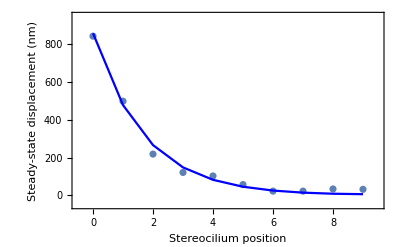

analwingindex = 3

wingindexnum = 6

S8731036_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.427258 | 0.00337796 | 126.484 | 5.85911×10^-10
Y0ss | 390.897 | 0.597545 | 654.171 | 1.5843×10^-13

AdjustedRSquared | 0.99697
AIC | 1020.47
BIC | 1020.3
RSquared | 0.997836

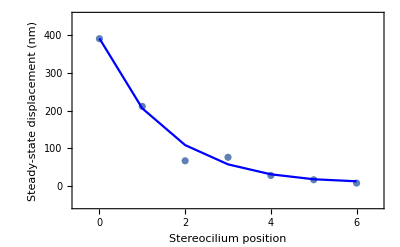

analwingindex = 4

wingindexnum = 7

S8731036_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.499242 | 0.0071189 | 70.129 | 1.11653×10^-8
Y0ss | 167.634 | 0.461368 | 363.342 | 2.99704×10^-12

AdjustedRSquared | 0.979181
AIC | 2260.18
BIC | 2260.02
RSquared | 0.985129

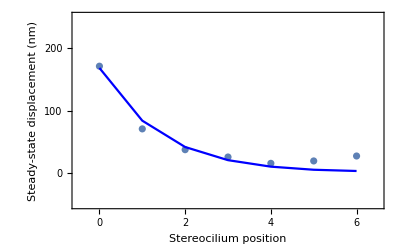

analwingindex = 5

wingindexnum = 8

S8731044_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.389159 | 0.00630939 | 61.6793 | 1.22087×10^-9
Y0ss | 203.51 | 0.679789 | 299.373 | 9.37464×10^-14

AdjustedRSquared | 0.984683
AIC | 1223.94
BIC | 1224.18
RSquared | 0.988513

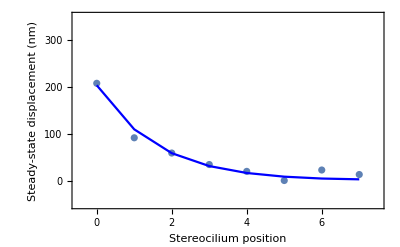

analwingindex = 6

wingindexnum = 9

S8731045_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.323449 | 0.00310621 | 104.13 | 5.28715×10^-11
Y0ss | 264.085 | 0.495478 | 532.99 | 2.94419×10^-15

AdjustedRSquared | 0.990781
AIC | 2253.27
BIC | 2253.51
RSquared | 0.993086

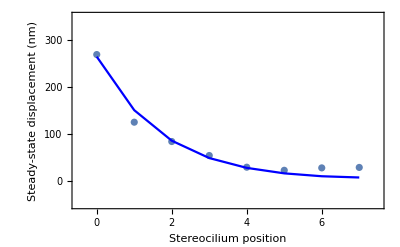

analwingindex = 7

wingindexnum = 10

S8731047_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.278512 | 0.00200512 | 138.901 | 3.66894×10^-10
Y0ss | 412.646 | 1.1819 | 349.137 | 3.65837×10^-12

AdjustedRSquared | 0.966551
AIC | 3831.02
BIC | 3830.86
RSquared | 0.976108

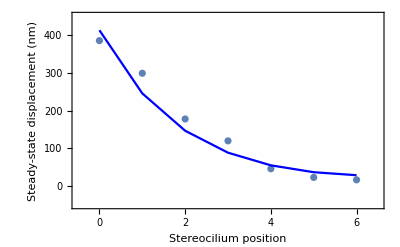

analwingindex = 8

wingindexnum = 11

S8731047_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.295559 | 0.00223258 | 132.384 | 4.66501×10^-10
Y0ss | 424.762 | 1.01824 | 417.151 | 1.50249×10^-12

AdjustedRSquared | 0.998967
AIC | 253.443
BIC | 253.281
RSquared | 0.999262

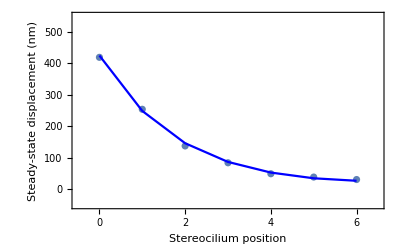

analwingindex = 9

wingindexnum = 13

S8802010_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.212211 | 0.0132493 | 16.0168 | 8.98189×10^-7
Y0ss | 62.0166 | 1.15096 | 53.8826 | 1.98783×10^-10

AdjustedRSquared | 0.984343
AIC | 73.6075
BIC | 74.1992
RSquared | 0.987822

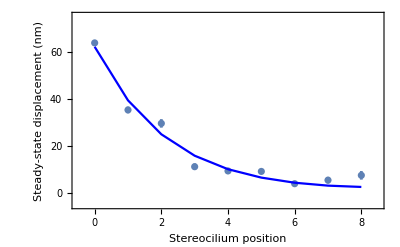

analwingindex = 10

wingindexnum = 14

S8802010_left_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.191542 | 0.00165254 | 115.908 | 2.78051×10^-11
Y0ss | 407.909 | 1.13773 | 358.527 | 3.17773×10^-14

AdjustedRSquared | 0.96804
AIC | 4023.08
BIC | 4023.32
RSquared | 0.97603

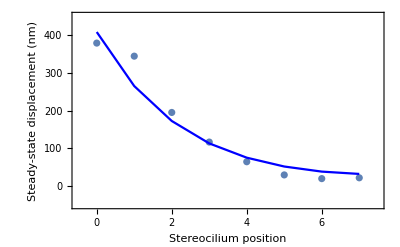

analwingindex = 11

wingindexnum = 15

S8802010_right_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.159703 | 0.001926 | 82.9194 | 9.76804×10^-12
Y0ss | 317.061 | 1.19436 | 265.465 | 2.84178×10^-15

AdjustedRSquared | 0.983266
AIC | 1266.05
BIC | 1266.64
RSquared | 0.986984

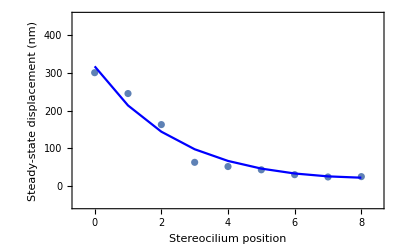

analwingindex = 12

wingindexnum = 16

S8802010_right_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.154369 | 0.000951494 | 162.238 | 8.91956×10^-14
Y0ss | 663.534 | 1.57801 | 420.488 | 1.13617×10^-16

AdjustedRSquared | 0.980587
AIC | 4653.31
BIC | 4653.9
RSquared | 0.984901

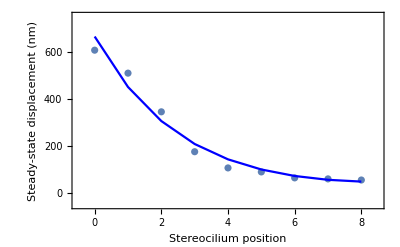

analwingindex = 13

wingindexnum = 17

S8802012_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.227344 | 0.00395393 | 57.4983 | 1.85912×10^-9
Y0ss | 103.944 | 0.443022 | 234.625 | 4.04519×10^-13

AdjustedRSquared | 0.985847
AIC | 700.202
BIC | 700.44
RSquared | 0.989385

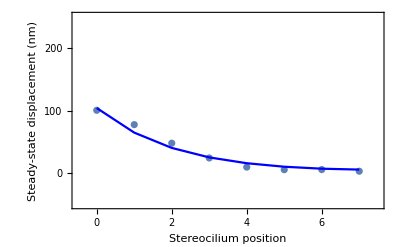

analwingindex = 14

wingindexnum = 18

S8802012_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.219477 | 0.00648348 | 33.8518 | 5.08716×10^-9
Y0ss | 71.692 | 0.486209 | 147.451 | 1.74103×10^-13

AdjustedRSquared | 0.978881
AIC | 476.098
BIC | 476.69
RSquared | 0.983574

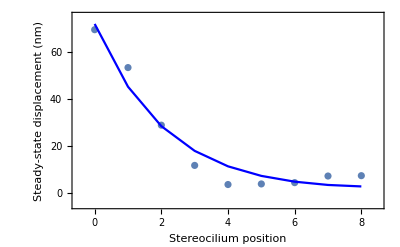

analwingindex = 15

wingindexnum = 20

S8804012_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.356876 | 0.0013824 | 258.156 | 1.35075×10^-9
Y0ss | 439.914 | 0.383159 | 1148.12 | 3.453×10^-12

AdjustedRSquared | 0.998388
AIC | 1602.41
BIC | 1601.79
RSquared | 0.998925

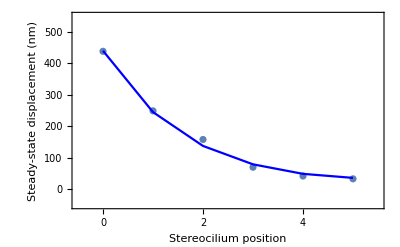

analwingindex = 16

wingindexnum = 21

S8804014_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.235891 | 0.000740855 | 318.404 | 6.83155×10^-8
Y0ss | 211.727 | 0.19485 | 1086.61 | 1.71887×10^-9

AdjustedRSquared | 0.996992
AIC | 2671.03
BIC | 2669.85
RSquared | 0.998195

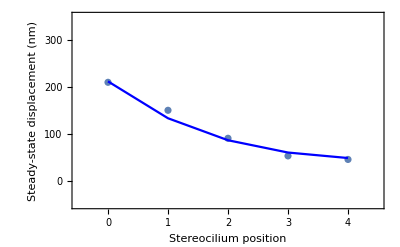

analwingindex = 17

wingindexnum = 22

S8804020_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.301667 | 0.0012111 | 249.084 | 1.55854×10^-9
Y0ss | 617.46 | 0.986045 | 626.198 | 3.90208×10^-11

AdjustedRSquared | 0.990997
AIC | 4115.41
BIC | 4114.78
RSquared | 0.993998

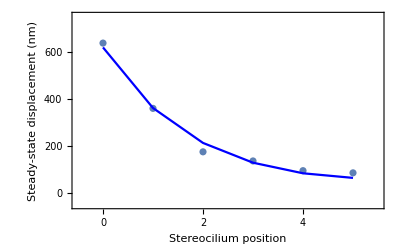

analwingindex = 18

wingindexnum = 24

S8807001_right_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.229074 | 0.00311881 | 73.449 | 1.31526×10^-12
Y0ss | 265.051 | 0.994446 | 266.531 | 4.39604×10^-17

AdjustedRSquared | 0.993007
AIC | 611.791
BIC | 612.699
RSquared | 0.994406

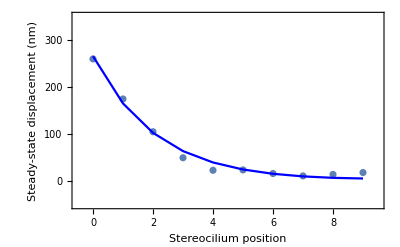

analwingindex = 19

wingindexnum = 25

S8807001_right_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.187506 | 0.00159919 | 117.25 | 3.12893×10^-14
Y0ss | 466.674 | 1.43236 | 325.807 | 8.81895×10^-18

AdjustedRSquared | 0.967909
AIC | 5300.42
BIC | 5301.33
RSquared | 0.974327

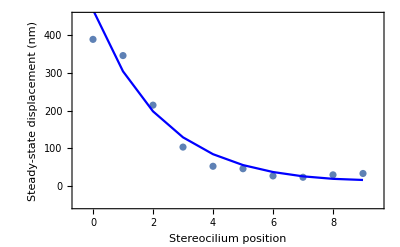

analwingindex = 20

wingindexnum = 26

S8807003_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.237612 | 0.00179167 | 132.62 | 3.65571×10^-13
Y0ss | 310.935 | 0.79452 | 391.35 | 1.87826×10^-16

AdjustedRSquared | 0.996661
AIC | 645.08
BIC | 645.672
RSquared | 0.997403

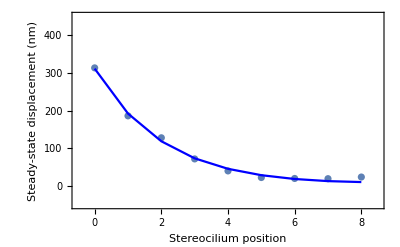

analwingindex = 21

wingindexnum = 27

S8807004_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.245501 | 0.00207314 | 118.42 | 2.89023×10^-14
Y0ss | 273.984 | 0.627564 | 436.584 | 8.48423×10^-19

AdjustedRSquared | 0.993181
AIC | 1403.23
BIC | 1404.14
RSquared | 0.994545

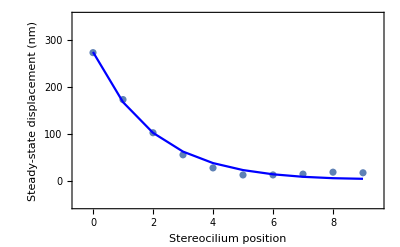

analwingindex = 22

wingindexnum = 28

S8807018_right_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.531762 | 0.00465741 | 114.175 | 1.04242×10^-12
Y0ss | 243.2 | 0.652126 | 372.934 | 2.63201×10^-16

AdjustedRSquared | 0.99514
AIC | 717.181
BIC | 717.773
RSquared | 0.99622

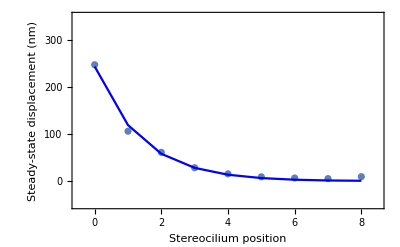

analwingindex = 23

wingindexnum = 29

S8808003_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.272787 | 0.0023767 | 114.775 | 2.94911×10^-11
Y0ss | 286.142 | 0.616681 | 464.003 | 6.76309×10^-15

AdjustedRSquared | 0.998576
AIC | 290.62
BIC | 290.858
RSquared | 0.998932

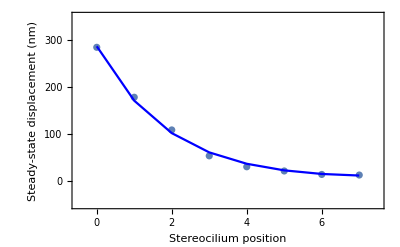

analwingindex = 24

wingindexnum = 30

S8809001_left_2

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.319201 | 0.00714069 | 44.7017 | 1.49764×10^-6
Y0ss | 203.576 | 1.33953 | 151.976 | 1.12443×10^-8

AdjustedRSquared | 0.970207
AIC | 623.738
BIC | 623.113
RSquared | 0.980138

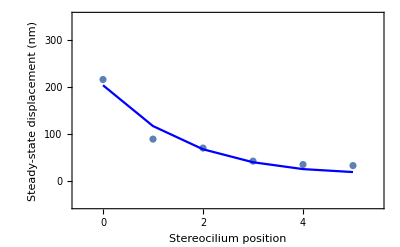

analwingindex = 25

wingindexnum = 31

S8809001_left_3

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.380194 | 0.00356776 | 106.564 | 1.82182×10^-6
Y0ss | 477.065 | 1.60076 | 298.024 | 8.33101×10^-8

AdjustedRSquared | 0.99056
AIC | 735.931
BIC | 734.76
RSquared | 0.994336

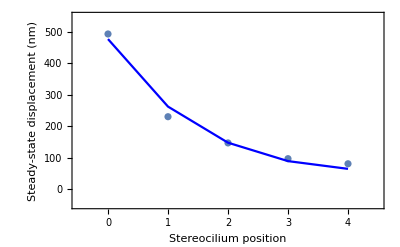

analwingindex = 26

wingindexnum = 32

S8809003_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.335064 | 0.00290199 | 115.46 | 9.2426×10^-10
Y0ss | 206.435 | 0.416942 | 495.116 | 6.37897×10^-13

AdjustedRSquared | 0.97283
AIC | 5645.6
BIC | 5645.44
RSquared | 0.980593

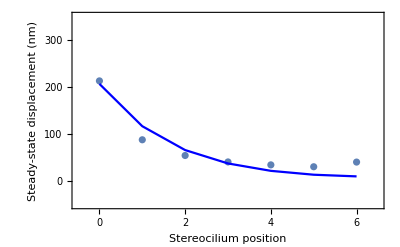

analwingindex = 27

wingindexnum = 33

S8809009_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.435486 | 0.0238972 | 18.2233 | 9.14659×10^-6
Y0ss | 45.5727 | 0.522195 | 87.2715 | 3.74395×10^-9

AdjustedRSquared | 0.997212
AIC | 32.1389
BIC | 31.9766
RSquared | 0.998009

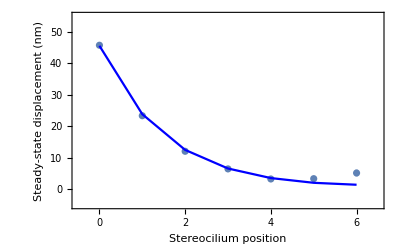

analwingindex = 28

wingindexnum = 34

S8809011_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.463083 | 0.0279725 | 16.5549 | 0.0000146837
Y0ss | 48.4728 | 0.693239 | 69.9222 | 1.13312×10^-8

AdjustedRSquared | 0.984236
AIC | 87.3517
BIC | 87.1894
RSquared | 0.98874

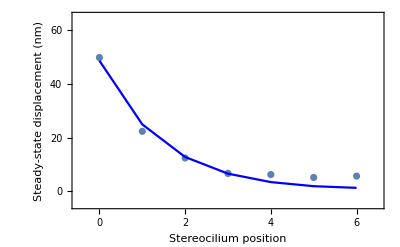

analwingindex = 29

wingindexnum = 35

S8811007_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.221985 | 0.00177416 | 125.122 | 6.18504×10^-10
Y0ss | 227.728 | 0.409797 | 555.708 | 3.58143×10^-13

AdjustedRSquared | 0.995926
AIC | 1137.5
BIC | 1137.34
RSquared | 0.99709

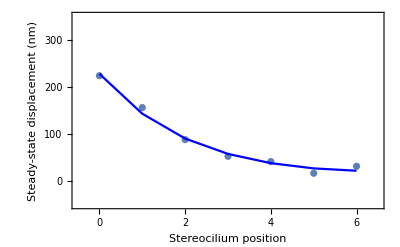

analwingindex = 30

wingindexnum = 36

S8811009_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.274105 | 0.00466447 | 58.7644 | 5.02177×10^-7
Y0ss | 103.706 | 0.483702 | 214.401 | 2.83909×10^-9

AdjustedRSquared | 0.993172
AIC | 277.472
BIC | 276.847
RSquared | 0.995448

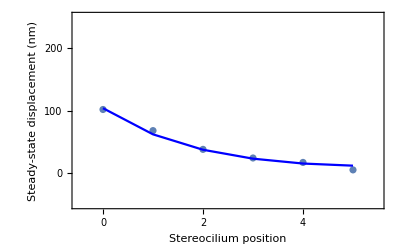

analwingindex = 31

wingindexnum = 37

S8811019_left_1

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.258281 | 0.00617247 | 41.844 | 1.24624×10^-8
Y0ss | 122.278 | 0.627342 | 194.914 | 1.23046×10^-12

AdjustedRSquared | 0.99866
AIC | 61.6965
BIC | 61.9349
RSquared | 0.998995

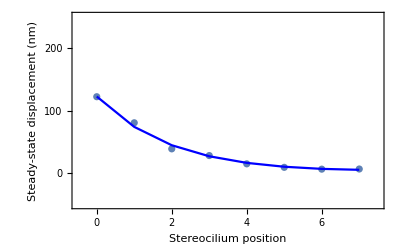

```mathematica
(*Fit wings with all positive onsets and ss*)
(*Index of analyzed wings*)
analwingindex = 0;
(*Fit weights are 1/SE^2 and there is a different number of points in each measurement window*)
For[wingindexnum = 1, wingindexnum ≤ Length[wingindex],wingindexnum++,
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
If[Length[Select[onset[[All,2]],#<0&]]+Length[Select[ss[[All,2]],#<0&]]>0,Continue[],analwingindex = analwingindex+1;Print["analwingindex = ",analwingindex];
Print["wingindexnum = ",wingindexnum];
ssErr=Table[{Data[[n,3]],Data[[n,11]]/Sqrt[Data[[n,10]]]},{n,wingindex[[wingindexnum]],If[wingindexnum+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum+1]]-1]}];
ssList[[wingindexnum]]=Join[{wingindexnum},{Table[{ss[[n,1]],Around[ss[[n,2]],ssErr[[n,2]]]},{n,1,Length[ss]}]}];
nstereo=Last[ss[[All,1]]]+1;
fit=NonlinearModelFit[Table[ss[[n,2]],{n,1,Length[ss]}],{YPW[AoL,m,nstereo,Y0ss]},{AoL,{Y0ss,ss[[1,2]]}},m,Weights->Table[1/ssErr[[n,2]]^2,{n,1,Length[ss]}],VarianceEstimatorFunction->(1&)];
ssnstereoList[[wingindexnum]]=nstereo;
ssAoLList[[wingindexnum,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
ssAoLList[[wingindexnum,2]]=Evaluate[fit["ParameterErrors"][[1]]];
ssAoLPvalList[[wingindexnum,2]]=Evaluate[fit["ParameterTable"][[1,1,2,5]]];
ssY0List[[wingindexnum,1,2]]=Evaluate[Y0ss/.fit["BestFitParameters"][[2]]];
ssY0List[[wingindexnum,2]]=Evaluate[fit["ParameterErrors"][[2]]];
ssY0PvalList[[wingindexnum,2]]=Evaluate[fit["ParameterTable"][[1,1,3,5]]];
ssAdjRsqList[[wingindexnum,2]]=Evaluate[fit["AdjustedRSquared"]];
ssExportTable[[wingindexnum,1]]=Data[[wingindex[[wingindexnum]],1]];
ssExportTable[[wingindexnum,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
ssExportTable[[wingindexnum,3]]=Evaluate[fit["ParameterErrors"][[1]]];
ssExportTable[[wingindexnum,4]]=Evaluate[Y0ss/.fit["BestFitParameters"][[2]]];
ssExportTable[[wingindexnum,5]]=Evaluate[fit["ParameterErrors"][[2]]];
ssExportTable[[wingindexnum,6]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum]],2]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = nstereo-1;
Ymin=0;
deltaY = 10^(MantissaExponent[ssList[[wingindexnum,2,1,2]]["Value"]+ssList[[wingindexnum,2,1,2]]["Uncertainty"]][[2]]-1);Ymax =Ceiling[ssList[[wingindexnum,2,1,2]]["Value"]+ssList[[wingindexnum,2,1,2]]["Uncertainty"],deltaY];
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Print[Show[ListPlot[ssList[[wingindexnum,2]],PlotRange->{{-0.5,Xmax+0.5},{-deltaY/2,Ymax+deltaY/2}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Steady-state displacement (nm)"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],ListPlot[Table[{ss[[n,1]],YPW[ssAoLList[[wingindexnum,1,2]],n,nstereo,ssY0List[[wingindexnum,1,2]]]},{n,1,Length[ss]}],PlotStyle->Blue,Joined->True]]]]]
```

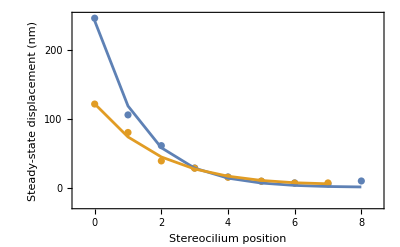

0.531762

0.258281

243.2

122.278

```mathematica
(*Example wings*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Max[Length[ssList[[wingindexnum1,2]]],Length[ssList[[wingindexnum2,2]]]]-1;
Ymin=0;
deltaY = 10^(MantissaExponent[Max[ssList[[wingindexnum1,2,1,2]]["Value"]+ssList[[wingindexnum1,2,1,2]]["Uncertainty"],ssList[[wingindexnum2,2,1,2]]["Value"]+ssList[[wingindexnum2,2,1,2]]["Uncertainty"]]][[2]]-1);Ymax =Ceiling[Max[ssList[[wingindexnum1,2,1,2]]["Value"]+ssList[[wingindexnum1,2,1,2]]["Uncertainty"],ssList[[wingindexnum2,2,1,2]]["Value"]+ssList[[wingindexnum2,2,1,2]]["Uncertainty"]],deltaY];
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Print[Show[ListPlot[{ssList[[wingindexnum1,2]],ssList[[wingindexnum2,2]]},PlotRange->{{-0.5,Xmax+0.5},{-deltaY/4,Ymax-deltaY/2}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Steady-state displacement (nm)"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],ListPlot[{Table[{ssList[[wingindexnum1,2,n,1]],YPW[ssAoLList[[wingindexnum1,1,2]],n,Length[ssList[[wingindexnum1,2]]],ssY0List[[wingindexnum1,1,2]]]},{n,1,Length[ssList[[wingindexnum1,2]]]}],Table[{ssList[[wingindexnum2,2,n,1]],YPW[ssAoLList[[wingindexnum2,1,2]],n,Length[ssList[[wingindexnum2,2]]],ssY0List[[wingindexnum2,1,2]]]},{n,1,Length[ssList[[wingindexnum2,2]]]}]},PlotStyle->Thickness[Linewidth],Joined->True]]]
ssAoLList[[wingindexnum1,1,2]]
ssAoLList[[wingindexnum2,1,2]]
ssY0List[[wingindexnum1,1,2]]
ssY0List[[wingindexnum2,1,2]]
```

```mathematica
(*****************Exported Data******************)
```

```mathematica
Data[[wingindex[[wingindexnum1]],1]]
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
ssErr=Table[{Data[[n,3]],Data[[n,11]]/Sqrt[Data[[n,10]]]},{n,wingindex[[wingindexnum1]],If[wingindexnum1+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum1+1]]-1]}];
nstereo=Last[ss[[All,1]]]+1;
fit=NonlinearModelFit[Table[ss[[n,2]],{n,1,Length[ss]}],{YPW[AoL,m,nstereo,Y0ss]},{AoL,{Y0ss,ss[[1,2]]}},m,Weights->Table[1/ssErr[[n,2]]^2,{n,1,Length[ss]}],VarianceEstimatorFunction->(1&)];
ssAoLList[[wingindexnum1,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
ssAoLList[[wingindexnum1,2]]=Evaluate[fit["ParameterErrors"][[1]]];
ssY0List[[wingindexnum1,1,2]]=Evaluate[Y0ss/.fit["BestFitParameters"][[2]]];
ssY0List[[wingindexnum1,2]]=Evaluate[fit["ParameterErrors"][[2]]];
ssAdjRsqList[[wingindexnum1,2]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum1]],1]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

S8807018_1_right

S8807018_1_right

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.531762 | 0.00465741 | 114.175 | 1.04242×10^-12
Y0ss | 243.2 | 0.652126 | 372.934 | 2.63201×10^-16

AdjustedRSquared | 0.99514
AIC | 717.181
BIC | 717.773
RSquared | 0.99622

```mathematica
Data[[wingindex[[wingindexnum2]],1]]
onset=Table[{Data[[n,3]],Data[[n,4]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
ss=Table[{Data[[n,3]],Data[[n,9]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
ssErr=Table[{Data[[n,3]],Data[[n,11]]/Sqrt[Data[[n,10]]]},{n,wingindex[[wingindexnum2]],If[wingindexnum2+1>Length[wingindex],Length[Data[[All,2]]],wingindex[[wingindexnum2+1]]-1]}];
nstereo=Last[ss[[All,1]]]+1;
fit=NonlinearModelFit[Table[ss[[n,2]],{n,1,Length[ss]}],{YPW[AoL,m,nstereo,Y0ss]},{AoL,{Y0ss,ss[[1,2]]}},m,Weights->Table[1/ssErr[[n,2]]^2,{n,1,Length[ss]}],VarianceEstimatorFunction->(1&)];
ssAoLList[[wingindexnum2,1,2]]=Evaluate[AoL/.fit["BestFitParameters"][[1]]];
ssAoLList[[wingindexnum2,2]]=Evaluate[fit["ParameterErrors"][[1]]];
ssY0List[[wingindexnum2,1,2]]=Evaluate[Y0ss/.fit["BestFitParameters"][[2]]];
ssY0List[[wingindexnum2,2]]=Evaluate[fit["ParameterErrors"][[2]]];
ssAdjRsqList[[wingindexnum2,2]]=Evaluate[fit["AdjustedRSquared"]];
Print[Data[[wingindex[[wingindexnum2]],1]]];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

S8811019_1_left

S8811019_1_left

| Estimate | Standard Error | t-Statistic | P-Value
AoL | 0.258281 | 0.00617247 | 41.844 | 1.24624×10^-8
Y0ss | 122.278 | 0.627342 | 194.914 | 1.23046×10^-12

AdjustedRSquared | 0.99866
AIC | 61.6965
BIC | 61.9349
RSquared | 0.998995

```mathematica
(*Remove NaN entries*)
baddata[entry_]:=MatchQ[entry,{{_?NumberQ,NaN},NaN}];
ssnstereoListrenum=DeleteCases[ssnstereoList,NaN];
ssAoLListtemp=DeleteCases[ssAoLList,_?baddata];
ssAoLListrenum=Table[{{n,ssAoLListtemp[[n,1,2]]},ssAoLListtemp[[n,2]]},{n,1,Length[ssAoLListtemp]}];
baddata2[entry_]:=MatchQ[entry,{_?NumberQ,NaN}];
ssAdjRsqListtemp=DeleteCases[ssAdjRsqList,_?baddata2];
ssAdjRsqListrenum=Table[{{n,ssAdjRsqListtemp[[n,2]]}},{n,1,Length[ssAdjRsqListtemp]}];
```

```mathematica
(*Minimum and maximum ratios*)
Min[ssAoLListrenum[[All,1,2]]]
Max[ssAoLListrenum[[All,1,2]]]
```

0.154369

0.531762

```mathematica
MedianSSAoL = Quantile[ssAoLListrenum[[All,1,2]],0.5]
LowerQuantileSSAoL = Quantile[ssAoLListrenum[[All,1,2]],0.25]
UpperQuantileSSAoL = Quantile[ssAoLListrenum[[All,1,2]],0.75]
```

0.278512

0.227344

0.358482

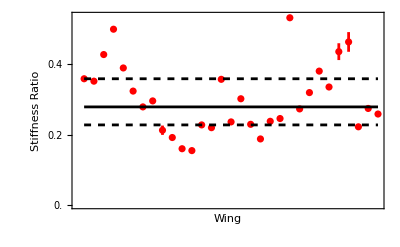

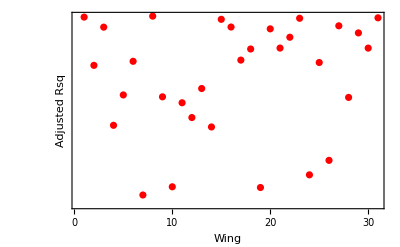

```mathematica
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Length[ssAoLListrenum];
Ymin=0;Ymax =1;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,5}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,0.1}];
Show[ListPlot[Table[{ssAoLListrenum[[n,1,1]],Around[ssAoLListrenum[[n,1,2]],ssAoLListrenum[[n,2]]]},{n,1,Length[ssAoLListrenum]}],PlotRange->All,PlotStyle->{Thickness[Linewidth],Red},IntervalMarkersStyle->{Thickness[Linewidth],Red},Frame->{{True,False},{True,False}},FrameTicks->{None,YTicks},FrameLabel->{"Wing","Stiffness Ratio"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[{MedianSSAoL,LowerQuantileSSAoL,UpperQuantileSSAoL},{n,1,Length[ssAoLListrenum]},PlotStyle->{{Thickness[Linewidth],Black},{Thickness[Linewidth],Black,Dashed},{Thickness[Linewidth],Black,Dashed}}]]
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Length[ssAoLListrenum];
Ymin=0;
Ymax =1;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,5}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,0.01}];
ListPlot[Table[{ssAoLListrenum[[n,1,1]],ssAdjRsqListrenum[[n,1,2]]},{n,1,Length[ssAoLListrenum]}],PlotRange->All,PlotStyle->{Thickness[Linewidth],Red},IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Wing","Adjusted Rsq"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(*Minimum adjRsq*)
Min[ssAdjRsqList[[All,2]]]
```

Min[0.966551,NaN]

```mathematica
(*Maximum P-value over all fit parameters*)
Max[{ssAoLPvalList[[All,2]],ssY0PvalList[[All,2]]}]
```

Max[0.0000146837,NaN]

```mathematica
SEList=DeleteCases[Table[onsetAoLList[[n,2]],{n,1,Length[wingindex]}],NaN];
onsetAoLList2=DeleteCases[onsetAoLList[[All,1,2]],NaN];
gammaAoLave =Sum[onsetAoLList2[[n]]/SEList[[n]]^2,{n,1,Length[onsetAoLList2]}]/Sum[1/SEList[[n]]^2,{n,1,Length[onsetAoLList2]}]
(*SE in the weighted mean*)
Sqrt[1/Sum[1/SEList[[n]]^2,{n,1,Length[onsetAoLList2]}]]
(*Fraction of wings above the mean => distribution is not symmetric*)
N[Sum[If[onsetAoLList2[[n]]>gammaAoLave,1,0],{n,1,Length[onsetAoLList2]}]/Length[onsetAoLList2]]
```

0.179818

0.000559756

0.677419

```mathematica
(*Average KA/KL with SE. Weighted mean, more weight when SE is smaller*)
SEList=DeleteCases[Table[ssAoLList[[n,2]],{n,1,Length[wingindex]}],NaN];
ssAoLList2=DeleteCases[ssAoLList[[All,1,2]],NaN];
KAoLave = Sum[ssAoLList2[[n]]/SEList[[n]]^2,{n,1,Length[ssAoLList2]}]/Sum[1/SEList[[n]]^2,{n,1,Length[ssAoLList2]}]
(*SE in the weighted mean*)
Sqrt[1/Sum[1/SEList[[n]]^2,{n,1,Length[ssAoLList2]}]]
(*Fraction of wings above the mean => distribution is not symmetric*)
N[Sum[If[ssAoLList2[[n]]>KAoLave,1,0],{n,1,Length[ssAoLList2]}]/Length[ssAoLList2]]
```

0.256637

0.0003463

0.612903

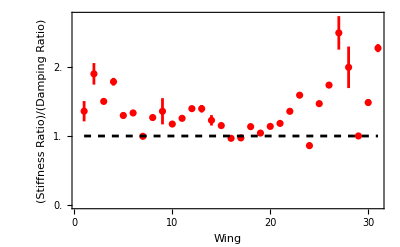

```mathematica
(*Predicts which wings overshoot for an ideal step stimulus (Ratio/Ratio > 1), but expt step is not ideal and probe drifts after onset.*)
RatioErr=Table[Abs[(ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]])*Sqrt[(onsetAoLListrenum[[n,2]]/onsetAoLListrenum[[n,1,2]])^2+(ssAoLListrenum[[n,2]]/ssAoLListrenum[[n,1,2]])^2]],{n,1,Length[ssAoLListrenum]}];
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = Length[ssAoLListrenum];
Ymin=0;
Ymax =5;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,5}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,0.5}];
Show[ListPlot[Table[{n,Around[ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]],RatioErr[[n]]]},{n,1,Length[ssAoLListrenum]}],PlotRange->All,PlotStyle->{Thickness[Linewidth],Red},IntervalMarkersStyle->{Thickness[Linewidth],Red},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Wing","(Stiffness Ratio)/(Damping Ratio)"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[1,{n,1,Length[ssAoLListrenum]},PlotStyle->{{Thickness[Linewidth],Black,Dashed}}]]
```

```mathematica
(*4 of 31 have ssAoL < onsetAoL => no overshoot for ideal step*)
Sum[{{ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]]<1}},{n,1,Length[ssAoLListrenum]}]
Table[{{n,ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]]}},{n,1,Length[ssAoLListrenum]}]
```

{{27 False+4 True}}

{{{1,1.36016}},{{2,1.90209}},{{3,1.50212}},{{4,1.7878}},{{5,1.29781}},{{6,1.33456}},{{7,0.995628}},{{8,1.26779}},{{9,1.35907}},{{10,1.1736}},{{11,1.25649}},{{12,1.39694}},{{13,1.39599}},{{14,1.22753}},{{15,1.15155}},{{16,0.966437}},{{17,0.972563}},{{18,1.13574}},{{19,1.04282}},{{20,1.13948}},{{21,1.18289}},{{22,1.35828}},{{23,1.59226}},{{24,0.860208}},{{25,1.46942}},{{26,1.73847}},{{27,2.49625}},{{28,1.99679}},{{29,1.00086}},{{30,1.48588}},{{31,2.27514}}}

```mathematica
(*Number of wings with KAoL > gammaAoL => Get overshoot for step stimulus.*)
Length[Cases[Table[ssAoLList[[n,1,2]]/onsetAoLList[[n,1,2]],{n,1,Length[wingindex]}],x_/;x>1]]
```

27

```mathematica
(*Weighted mean of RatioRatio, more weight when SE is smaller*)
RatioRatioList=DeleteCases[Table[ssAoLList[[n,1,2]]/onsetAoLList[[n,1,2]],{n,1,Length[wingindex]}],NaN];
SERatioRatioList=DeleteCases[Table[(ssAoLList[[n,1,2]]/onsetAoLList[[n,1,2]])*Sqrt[(ssAoLList[[n,2]]/ssAoLList[[n,1,2]])^2+(onsetAoLList[[n,2]]/onsetAoLList[[n,1,2]])^2],{n,1,Length[wingindex]}],NaN];
wmean=Sum[RatioRatioList[[n]]/SERatioRatioList[[n]]^2,{n,1,Length[RatioRatioList]}]/Sum[1/SERatioRatioList[[n]]^2,{n,1,Length[RatioRatioList]}]
(*SE in the weighted mean*)
sewmean=Sqrt[1/Sum[1/SERatioRatioList[[n]]^2,{n,1,Length[RatioRatioList]}]]
```

1.13437

0.00403623

```mathematica
Length[RatioRatioList]
```

31

```mathematica
(*Means don't give the full picture, because distributions are not symmetric*)
(*Ave[KAoL/gammaAoL] < Ave[KAoL]/Ave[gammaAoL]*)
wmean
KAoLave/gammaAoLave
(*Fraction of wings above the mean*)
N[Sum[If[RatioRatioList[[n]]>wmean,1,0],{n,1,Length[RatioRatioList]}]/Length[RatioRatioList]]
```

1.13437

1.42721

0.806452

```mathematica
(*Median is better for non-symmetric data*)
gammaAoLmedian = Median[onsetAoLList2]
KAoLmedian =Median[ssAoLList2]
KAoLOgammaAoLmedian =Median[RatioRatioList]
(*Fraction of wings above the median of ratios*)
N[Sum[If[RatioRatioList[[n]]>KAoLOgammaAoLmedian,1,0],{n,1,Length[RatioRatioList]}]/Length[RatioRatioList]]
```

0.208526

0.278512

1.33456

0.483871

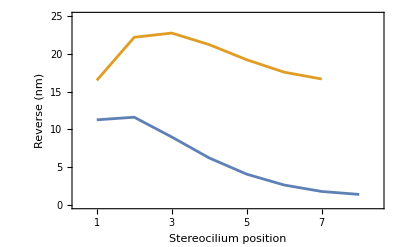

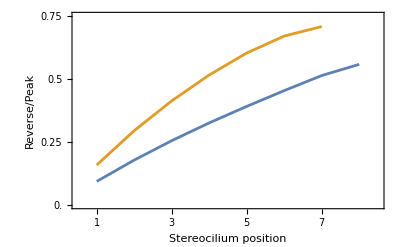

0.531762

0.258281

0.391498

0.113523

243.2

223.285

122.278

144.43

```mathematica
(*Reversal for ideal step using fit values. Use Y0 from onset*)
(*Example wings*)
wingindexnum1 = 28;
wingindexnum2 = 37;
(*Reversal = Peak - Steady-state*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = Max[Length[ssList[[wingindexnum1,2]]],Length[ssList[[wingindexnum2,2]]]]-1;
Ymin=0;
deltaY = 5;
Ymax =25;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Show[ListPlot[{Table[{ssList[[wingindexnum1,2,n,1]],YPW[onsetAoLList[[wingindexnum1,1,2]],n,Length[onsetList[[wingindexnum1,2]]],onsetY0List[[wingindexnum1,1,2]]]-YPW[ssAoLList[[wingindexnum1,1,2]],n,Length[ssList[[wingindexnum1,2]]],onsetY0List[[wingindexnum1,1,2]]]},{n,2,Length[ssList[[wingindexnum1,2]]]}],Table[{ssList[[wingindexnum2,2,n,1]],YPW[onsetAoLList[[wingindexnum2,1,2]],n,Length[onsetList[[wingindexnum2,2]]],onsetY0List[[wingindexnum2,1,2]]]-YPW[ssAoLList[[wingindexnum2,1,2]],n,Length[ssList[[wingindexnum2,2]]],onsetY0List[[wingindexnum2,1,2]]]},{n,2,Length[ssList[[wingindexnum2,2]]]}]},PlotRange->{{Xmin-0.5,Xmax+0.5},{0,Ymax}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Reverse (nm)"},Joined->True,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
(*Reversal/Peak = 1 - Steady-state/Peak*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = Max[Length[ssList[[wingindexnum1,2]]],Length[ssList[[wingindexnum2,2]]]]-1;
Ymin=0;
deltaY = 0.25;
Ymax =0.75;
Linewidth = 0.005;
Fontsize = 12;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,deltaY}];
Show[ListPlot[{Table[{ssList[[wingindexnum1,2,n,1]],1-YPW[ssAoLList[[wingindexnum1,1,2]],n,Length[ssList[[wingindexnum1,2]]],onsetY0List[[wingindexnum1,1,2]]]/YPW[onsetAoLList[[wingindexnum1,1,2]],n,Length[onsetList[[wingindexnum1,2]]],onsetY0List[[wingindexnum1,1,2]]]},{n,2,Length[ssList[[wingindexnum1,2]]]}],Table[{ssList[[wingindexnum2,2,n,1]],1-YPW[ssAoLList[[wingindexnum2,1,2]],n,Length[ssList[[wingindexnum2,2]]],onsetY0List[[wingindexnum2,1,2]]]/YPW[onsetAoLList[[wingindexnum2,1,2]],n,Length[onsetList[[wingindexnum2,2]]],onsetY0List[[wingindexnum2,1,2]]]},{n,2,Length[ssList[[wingindexnum2,2]]]}]},PlotRange->{{Xmin-0.5,Xmax+0.5},{0,Ymax}},PlotStyle->Thickness[Linewidth],IntervalMarkersStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Reverse/Peak"},Joined->True,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
ssAoLList[[wingindexnum1,1,2]]
ssAoLList[[wingindexnum2,1,2]]
onsetAoLList[[wingindexnum1,1,2]]
onsetAoLList[[wingindexnum2,1,2]]
ssY0List[[wingindexnum1,1,2]]
onsetY0List[[wingindexnum1,1,2]]
ssY0List[[wingindexnum2,1,2]]
onsetY0List[[wingindexnum2,1,2]]
```

```mathematica
ntotv = ssnstereoList[[wingindexnum1]];
KAoLv = ssAoLList[[wingindexnum1,1,2]];
gammaAoLv = onsetAoLList[[wingindexnum1,1,2]];
KAoLv/gammaAoLv
Y0v = 500;(*nm*)
```

1.35828

| Estimate | Standard Error | t-Statistic | P-Value
ndec | -1.62611 | 0.00411952 | -394.732 | 1.89986×10^-18

AdjustedRSquared | 0.999984
AIC | -87.261
BIC | -86.8665
RSquared | 0.999985

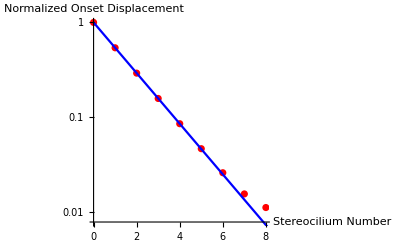

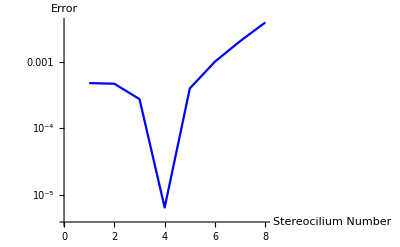

```mathematica
(*Onset decay can be fit by an exponential. Deviates from exponential at stereocilium numbers close to ntot*)
fit=NonlinearModelFit[Table[{n,Y[n,ntotv,gammaAoLv,Y0v]/Y0v},{n,0,ntotv-1}],{Exp[m/ndec]},{{ndec,-1}},m];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
Show[ListLogPlot[Table[{n,Y[n,ntotv,gammaAoLv,Y0v]/Y0v},{n,0,ntotv-1}],PlotStyle->Red,AxesLabel->{"Stereocilium Number","Normalized Onset Displacement"},AxesStyle->Directive[Black,FontSize->12]],ListLogPlot[Table[{n,Exp[n/(ndec/.fit["BestFitParameters"])]},{n,0,ntotv}],PlotStyle->Blue,Joined->True]]
(*Absolute error between exact solution and exponential fit*)
ListLogPlot[Table[{n,Abs[Y[n,ntotv,gammaAoLv,Y0v]/Y0v-Exp[n/(ndec/.fit["BestFitParameters"])]]},{n,0,ntotv-1}],PlotStyle->Blue,Joined->True,AxesLabel->{"Stereocilium Number","Error"},AxesStyle->Directive[Black,FontSize->12,PlotRange->All]]
```

| Estimate | Standard Error | t-Statistic | P-Value
ndec | -1.40119 | 0.00155432 | -901.483 | 2.56768×10^-21

AdjustedRSquared | 0.999997
AIC | -103.511
BIC | -103.116
RSquared | 0.999997

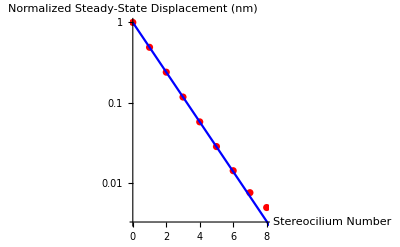

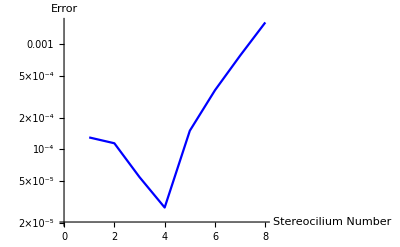

```mathematica
(*ss decay can be fit by an exponential. Deviates from exponential at stereocilium numbers close to ntot*)
fit=NonlinearModelFit[Table[{n,Y[n,ntotv,KAoLv,Y0v]/Y0v},{n,0,ntotv-1}],{Exp[m/ndec]},{{ndec,-1}},m];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
Show[ListLogPlot[Table[{n,Y[n,ntotv,KAoLv,Y0v]/Y0v},{n,0,ntotv-1}],PlotStyle->Red,AxesLabel->{"Stereocilium Number","Normalized Steady-State Displacement (nm)"},AxesStyle->Directive[Black,FontSize->12]],ListLogPlot[Table[{n,Exp[n/(ndec/.fit["BestFitParameters"])]},{n,0,ntotv}],PlotStyle->Blue,Joined->True]]
(*Absolute error between exact solution and exponential fit*)ListLogPlot[Table[{n,Abs[Y[n,ntotv,KAoLv,Y0v]/Y0v-Exp[n/(ndec/.fit["BestFitParameters"])]]},{n,0,ntotv-1}],PlotStyle->Blue,Joined->True,AxesLabel->{"Stereocilium Number","Error"},AxesStyle->Directive[Black,FontSize->12]]
```

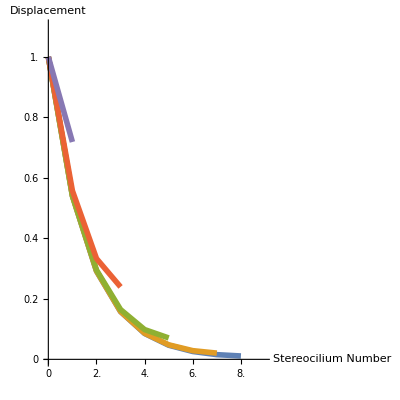

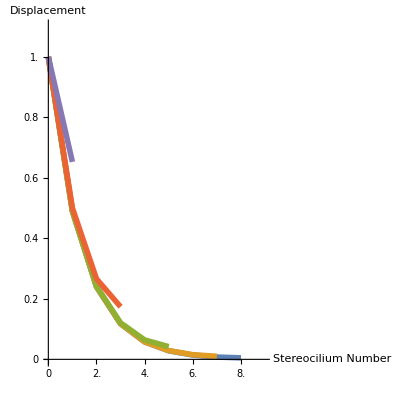

```mathematica
(*Note that the onset and ss decays depend on the total number of stereocilia even when normalized*)
Y0v = 500;
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = ntotv;
Ymin=0;
Ymax =1.1;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,2*10^0}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,2*10^-1}];
(*Onset*)
ListPlot[{Table[{n,Y[n,ntotv,gammaAoLv,Y0v]/Y0v},{n,0,ntotv-1}],Table[{n,Y[n,8,gammaAoLv,Y0v]/Y0v},{n,0,8-1}],Table[{n,Y[n,6,gammaAoLv,Y0v]/Y0v},{n,0,6-1}],Table[{n,Y[n,4,gammaAoLv,Y0v]/Y0v},{n,0,4-1}],Table[{n,Y[n,2,gammaAoLv,Y0v]/Y0v},{n,0,2-1}]},AspectRatio->1,PlotRange->{{0,ntotv},{0,1.1}},PlotStyle->Thickness[0.01],AxesLabel->{"Stereocilium Number","Displacement"},AxesStyle->Directive[Black,FontSize->12],Ticks->{XTicks,YTicks},Method->{"AxesInFront"->False},Joined->True]
(*ss*)
ListPlot[{Table[{n,Y[n,ntotv,KAoLv,Y0v]/Y0v},{n,0,ntotv-1}],Table[{n,Y[n,8,KAoLv,Y0v]/Y0v},{n,0,8-1}],Table[{n,Y[n,6,KAoLv,Y0v]/Y0v},{n,0,6-1}],Table[{n,Y[n,4,KAoLv,Y0v]/Y0v},{n,0,4-1}],Table[{n,Y[n,2,KAoLv,Y0v]/Y0v},{n,0,2-1}]},AspectRatio->1,PlotRange->{{0,ntotv},{0,1.1}},PlotStyle->Thickness[0.01],AxesLabel->{"Stereocilium Number","Displacement"},AxesStyle->Directive[Black,FontSize->12],Ticks->{XTicks,YTicks},Method->{"AxesInFront"->False},Joined->True]
```

```mathematica
(***************)
(*Simulate Step Stimulus*)
(***************)
```

```mathematica
(*Slope of the stimulus onset used heres. s/4 is the maximum slope.*)
slopef[t_,tS_,s_]:=Evaluate[D[(1+Exp[-(t-tS)*s])^-1,t]]
slopef[t,tS,s]
(*Find time of maximum slope*)
Dslopef[t_,tS_,s_]:=Evaluate[D[slopef[t,tS,s],t]]
Solve[Dslopef[t,tS,s]==0,t,Reals]
(*Maximum slope*)
slopef[tS,tS,s]
```

(ⅇ^(s (-t+tS)) s)/((1+ⅇ^(s (-t+tS)))^2)

{{t→tS}}

s/4

```mathematica
(***************)
(*wingindexnum2*)
(***************)
```

8

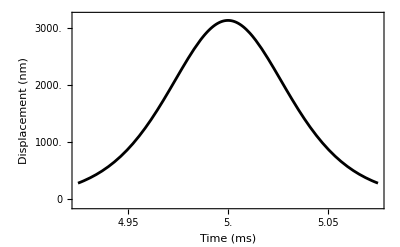

```mathematica
(*Match slope of stimulus to experimental data*)
ntotv = ssnstereoList[[wingindexnum2]]
Y0v = 250 (*nm*);
slopefac = 50;
ts = 5;
te = 55;
trange = 60;
Y0f[t_] := Y0v*Evaluate[(1+Exp[-(t-ts)*slopefac])^-1-(1+Exp[-(t-te)*slopefac])^-1];
(*Tick Marks*)
TickLength = 0.02;
Xmin = ts-0.1;
Xmax = ts+0.1;
Ymin=0;
Ymax =5*10^3;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,5*10^-2}];
YTicks=Table[{i,N[i,1],{0,TickLength}},{i,Ymin,Ymax,10^3}];
Show[Plot[{Y0f'[t]},{t,ts-0.075,ts+0.075},PlotRange->{-100,3.2*10^3},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

0.8

0.670773

{{Y1→InterpolatingFunction[…],Y2→InterpolatingFunction[…],Y3→InterpolatingFunction[…],Y4→InterpolatingFunction[…],Y5→InterpolatingFunction[…],Y6→InterpolatingFunction[…],Y7→InterpolatingFunction[…]}}

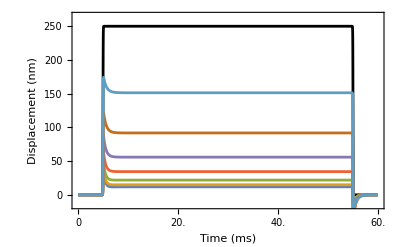

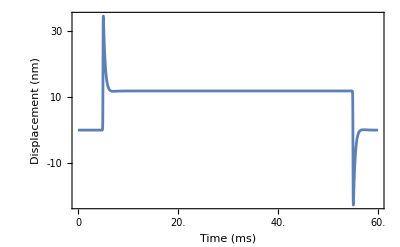

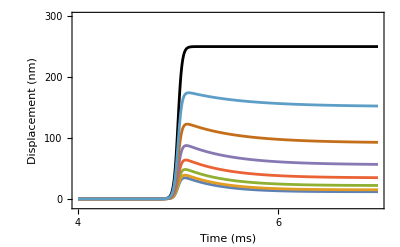

```mathematica
(*Doesn't work unless we use the equation simplification method*)
(*8 cilia, Y0 clamped, all cilia have rootlets. For 10 kHz low-pass filtered experimental stimulus use s = 10*4 = 40 such that the maximum slope is 5 kHz.*)
KLv = 5;(*mN/m*)
KAv = ssAoLList[[wingindexnum2,1,2]]*KLv;
gammaLv = 0.8*KLv;(*uN.s/m*)
gammaLv/KLv(*ms*)
gammaAv = onsetAoLList[[wingindexnum2,1,2]]*gammaLv;
KAoLv = KAv/KLv;
gammaAoLv = gammaAv/gammaLv;
(*Geometric mean time constant*)
taugmv =(gammaLv/KLv)*(g[ntotv-1,gammaAoLv,1]/g[ntotv-1,KAv/KLv,1])^(1/(ntotv-1))
KA1v = KAv;gammaA1v =gammaAv;
KA2v = KAv;gammaA2v =gammaAv;
KA3v = KAv;gammaA3v =gammaAv;
KA4v = KAv;gammaA4v =gammaAv;
KA5v = KAv;gammaA5v =gammaAv;
KA6v = KAv;gammaA6v =gammaAv;
KA7v = KAv;gammaA7v =gammaAv;
K1v = KLv;gamma1v = gammaLv;
K2v = KLv;gamma2v = gammaLv;
K3v = KLv;gamma3v = gammaLv;
K4v = KLv;gamma4v = gammaLv;
K5v = KLv;gamma5v = gammaLv;
K6v = KLv;gamma6v = gammaLv;
K7v = KLv;gamma7v = gammaLv;
Ysln=NDSolve[{KA1v*Y1[t]+gammaA1v*Y1'[t]+K1v*(Y1[t]-Y0f[t])-K2v*(Y2[t]-Y1[t])+gamma1v*(Y1'[t]-Y0f'[t])-gamma2v*(Y2'[t]-Y1'[t])==0,Y1[0]==0,KA2v*Y2[t]+gammaA2v*Y2'[t]+K2v*(Y2[t]-Y1[t])-K3v*(Y3[t]-Y2[t])+gamma2v*(Y2'[t]-Y1'[t])-gamma3v*(Y3'[t]-Y2'[t])==0,Y2[0]==0,KA3v*Y3[t]+gammaA3v*Y3'[t]+K3v*(Y3[t]-Y2[t])-K4v*(Y4[t]-Y3[t])+gamma3v*(Y3'[t]-Y2'[t])-gamma4v*(Y4'[t]-Y3'[t])==0,Y3[0]==0,KA4v*Y4[t]+gammaA4v*Y4'[t]+K4v*(Y4[t]-Y3[t])-K5v*(Y5[t]-Y4[t])+gamma4v*(Y4'[t]-Y3'[t])-gamma5v*(Y5'[t]-Y4'[t])==0,Y4[0]==0,KA5v*Y5[t]+gammaA5v*Y5'[t]+K5v*(Y5[t]-Y4[t])-K6v*(Y6[t]-Y5[t])+gamma5v*(Y5'[t]-Y4'[t])-gamma6v*(Y6'[t]-Y5'[t])==0,Y5[0]==0,KA6v*Y6[t]+gammaA6v*Y6'[t]+K6v*(Y6[t]-Y5[t])-K7v*(Y7[t]-Y6[t])+gamma6v*(Y6'[t]-Y5'[t])-gamma7v*(Y7'[t]-Y6'[t])==0,Y6[0]==0,KA7v*Y7[t]+gammaA7v*Y7'[t]+K7v*(Y7[t]-Y6[t])+gamma7v*(Y7'[t]-Y6'[t])==0,Y7[0]==0},{Y1,Y2,Y3,Y4,Y5,Y6,Y7},{t,0,trange},Method->{"EquationSimplification"->"Residual"}]
Y1f[t_]:=Evaluate[Y1[t]/.Ysln[[1]]]
Y2f[t_]:=Evaluate[Y2[t]/.Ysln[[1]]]
Y3f[t_]:=Evaluate[Y3[t]/.Ysln[[1]]]
Y4f[t_]:=Evaluate[Y4[t]/.Ysln[[1]]]
Y5f[t_]:=Evaluate[Y5[t]/.Ysln[[1]]]
Y6f[t_]:=Evaluate[Y6[t]/.Ysln[[1]]]
Y7f[t_]:=Evaluate[Y7[t]/.Ysln[[1]]]
(*Stimulus and responses*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=0;
Ymax =250;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
Show[Plot[{Y0f[t]},{t,0,trange},PlotRange->{Ymin-15,Ymax+15},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
(*Decay rates are different.*)
Y1peak=Evaluate[NMaximize[{Y1f[t],t<trange/2,t>0},t][[1]]];
t1peak=Evaluate[t/.NMaximize[{Y1f[t],t<trange/2,t>0},t][[2]]];
Y2peak=Evaluate[NMaximize[{Y2f[t],t<trange/2,t>0},t][[1]]];
t2peak=Evaluate[t/.NMaximize[{Y2f[t],t<trange/2,t>0},t][[2]]];
Y3peak=Evaluate[NMaximize[{Y3f[t],t<trange/2,t>0},t][[1]]];
t3peak=Evaluate[t/.NMaximize[{Y3f[t],t<trange/2,t>0},t][[2]]];
Y4peak=Evaluate[NMaximize[{Y4f[t],t<trange/2,t>0},t][[1]]];
t4peak=Evaluate[t/.NMaximize[{Y4f[t],t<trange/2,t>0},t][[2]]];
Y5peak=Evaluate[NMaximize[{Y5f[t],t<trange/2,t>0},t][[1]]];
t5peak=Evaluate[t/.NMaximize[{Y5f[t],t<trange/2,t>0},t][[2]]];
Y6peak=Evaluate[NMaximize[{Y6f[t],t<trange/2,t>0},t][[1]]];
t6peak=Evaluate[t/.NMaximize[{Y6f[t],t<trange/2,t>0},t][[2]]];
Y7peak=Evaluate[NMaximize[{Y7f[t],t<trange/2,t>0},t][[1]]];
t7peak=Evaluate[t/.NMaximize[{Y7f[t],t<trange/2,t>0},t][[2]]];
(*Stereocilium 7 response*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=-50;
Ymax =50;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,1*10^1}];
stereocilium1symmplot=Show[Plot[{Y7f[t]},{t,0,trange},PlotRange->All,MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
(*Zoom for onset time*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = ts+3;
Ymin=0;
Ymax =300;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1*10^0}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,1*10^2}];
Show[Plot[{Y0f[t]},{t,ts-1,ts+2},PlotRange->{Ymin-10,Ymax},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,ts-1,ts+2},PlotRange->All,MaxRecursion-> 15,PlotStyle->{Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

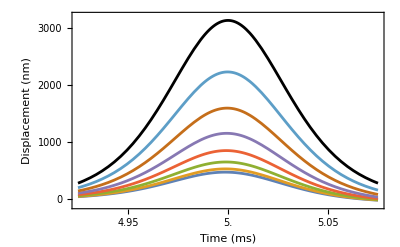

```mathematica
(*Tick Marks*)
TickLength = 0.02;
Xmin = ts-0.1;
Xmax = ts+0.1;
Ymin=0;
Ymax =5*10^3;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,5*10^-2}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,10^3}];
Show[Plot[{Y0f'[t]},{t,ts-0.075,ts+0.075},PlotRange->{-100,3.2*10^3},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[{Y7f'[t],Y6f'[t],Y5f'[t],Y4f'[t],Y3f'[t],Y2f'[t],Y1f'[t]},{t,ts-0.075,ts+0.075},PlotRange->{-100,3.2*10^3},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

```mathematica
(**************)
```

5.

4.99979

4.99958

4.99935

4.99913

4.9989

4.99871

4.99859

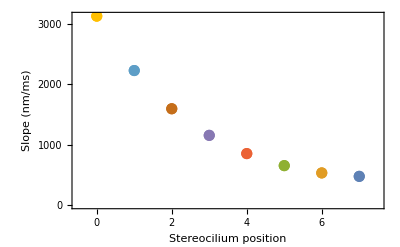

```mathematica
(*Plot maximum slope versus stereocilium position*)
Y0slopemax=Evaluate[NMaximize[{Y0f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t0slopemax=Evaluate[t/.NMaximize[{Y0f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y1slopemax=Evaluate[NMaximize[{Y1f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t1slopemax=Evaluate[t/.NMaximize[{Y1f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y2slopemax=Evaluate[NMaximize[{Y2f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t2slopemax=Evaluate[t/.NMaximize[{Y2f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y3slopemax=Evaluate[NMaximize[{Y3f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t3slopemax=Evaluate[t/.NMaximize[{Y3f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y4slopemax=Evaluate[NMaximize[{Y4f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t4slopemax=Evaluate[t/.NMaximize[{Y4f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y5slopemax=Evaluate[NMaximize[{Y5f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t5slopemax=Evaluate[t/.NMaximize[{Y5f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y6slopemax=Evaluate[NMaximize[{Y6f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t6slopemax=Evaluate[t/.NMaximize[{Y6f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
Y7slopemax=Evaluate[NMaximize[{Y7f'[t],t<ts+0.1,t>ts-0.1},t][[1]]];
t7slopemax=Evaluate[t/.NMaximize[{Y7f'[t],t<ts+0.1,t>ts-0.1},t][[2]]]
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = 7;
Ymin=0;
Ymax =5*10^3;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,Ymax*1*10^-1}];
ListPlot[{{{7,Y7slopemax}},{{6,Y6slopemax}},{{5,Y5slopemax}},{{4,Y4slopemax}},{{3,Y3slopemax}},{{2,Y2slopemax}},{{1,Y1slopemax}},{{0,Y0slopemax}}},PlotRange->{{Xmin-0.5,Xmax+0.5},{Ymin,All}},PlotStyle->Table[{ColorData[97,"ColorList"][[n]],PointSize[0.02]},{n,1,10}],PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Stereocilium position","Slope (nm/ms)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

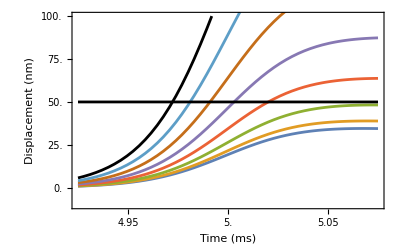

```mathematica
(*Zoom for time to fixed displacement*)
Yth = 50;
(*Tick Marks*)
TickLength = 0.02;
Xmin = ts-0.1;
Xmax = ts+0.1;
Ymin=0;
Ymax =100;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,5*10^-2}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,2.5*10^1}];
Show[Plot[{Y0f[t]},{t,ts-0.075,ts+0.075},PlotRange->{Ymin-10,Ymax},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,ts-0.075,ts+0.075},PlotRange->All,MaxRecursion-> 15,PlotStyle->{Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],Plot[Yth,{t,ts-0.075,ts+0.075},PlotStyle->{Black,Thickness[Linewidth]}]]
```

```mathematica
(*Time to absolute displacement lags for noncontacted stereocilia - see unnormalized onset zoom. Find time to fixed displacement.*)
(*NaN if Yth is not achieved*)
deltat = 10^-5;
tmin = ts-0.1;
tmax = ts+0.1;
ttable=Table[t,{t,tmin,tmax,deltat}];
t0max=If[Total[Table[If[Y0f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y0f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y0f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];t1max=If[Total[Table[If[Y1f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y1f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y1f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t2max=If[Total[Table[If[Y2f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y2f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y2f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t3max=If[Total[Table[If[Y3f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y3f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y3f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t4max=If[Total[Table[If[Y4f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y4f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y4f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t5max=If[Total[Table[If[Y5f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y5f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y5f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t6max=If[Total[Table[If[Y6f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y6f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y6f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
t7max=If[Total[Table[If[Y7f[t]-Yth>0,1,0],{t,tmin,tmax,deltat}]]>0,ttable[[Flatten[Position[Table[Abs[Y7f[t]-Yth],{t,tmin,tmax,deltat}],Min[Table[Abs[Y7f[t]-Yth],{t,tmin,tmax,deltat}]]]]]][[1]],NaN];
{t0max,t1max,t2max,t3max,t4max,t5max,t6max,t7max}
```

{4.97227,4.98109,4.99101,5.00303,5.02013,NaN,NaN,NaN}

```mathematica
(*Delay relative to stimulated stereocilium increases with stereocilium position*)
{{{1,t1max-t0max}},{{2,t2max-t0max}},{{3,t3max-t0max}},{{4,t4max-t0max}},{{5,t5max-t0max}},{{6,t6max-t0max}},{{7,t7max-t0max}}}
```

{{{1,0.00882}},{{2,0.01874}},{{3,0.03076}},{{4,0.04786}},{{5,NaN}},{{6,NaN}},{{7,NaN}}}

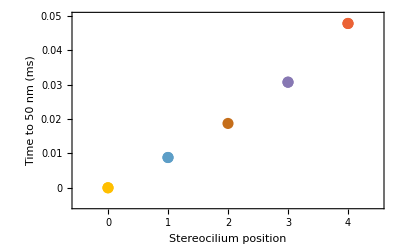

```mathematica
(*Responses lag stimulus*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = 4;
Ymin=0;
Ymax =0.05;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-2}];
ListPlot[{{{0,t0max-t0max}},{{1,t1max-t0max}},{2,t2max-t0max},{{3,t3max-t0max}},{{4,t4max-t0max}}},PlotRange->{{Xmin-0.5,Xmax+0.5},{Ymin-0.005,Ymax}},PlotStyle->Table[{ColorData[97,"ColorList"][[n]],PointSize[0.02]},{n,8,1,-1}],Frame->{{True,False},{True,False}},FrameLabel->{"Stereocilium position","Time to 50 nm (ms)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(*There are ntotv-1 time constants. Roots are time constants.*)
```

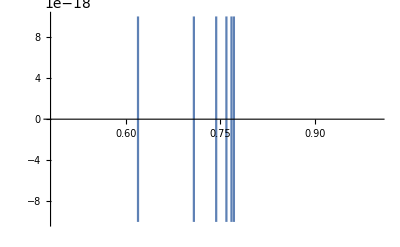

```mathematica
Plot[g[ntotv-1,-tau*KAv + gammaAv,-tau*KLv + gammaLv],{tau,0.48,1},PlotRange->{-10^-17,10^-17}]
```

```mathematica
(*Find effective time constants from fitting. 1 time constant is sufficient. 2 time constants doesn't work.*)
```

```mathematica
taufit = Table[NaN,{n,1,ntotv-1}];
```

```mathematica
(*Time after peak to fit*)
tfitend = 5;
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.352212 | 0.00448972 | 78.4486 | 3.52386×10^-53
A | 23.4182 | 0.18434 | 127.038 | 2.18774×10^-63

AdjustedRSquared | 0.997987
AIC | -3.98866
BIC | 1.80681
RSquared | 0.998066

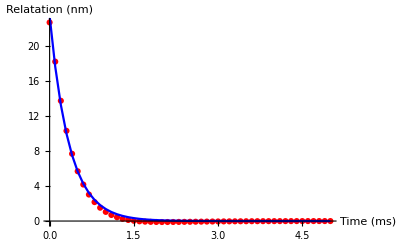

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 12.6489 | 69.9233 | 0.180896 | 0.857227
tau1 | 0.352212 | 3.06055×10^8 | 1.15081×10^-9 | 1
A2 | 10.7693 | 70.0085 | 0.153829 | 0.878403
tau2 | 0.352212 | 3.5947×10^8 | 9.79811×10^-10 | 1

AdjustedRSquared | 0.997901
AIC | 0.136645
BIC | 9.79577
RSquared | 0.998066

```mathematica
Yfittable = Table[{t,Y7f[t+t7peak]-Y[7,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[7]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.370121 | 0.00387719 | 95.4611 | 2.4946×10^-57
A | 24.6955 | 0.160756 | 153.621 | 2.02638×10^-67

AdjustedRSquared | 0.998636
AIC | -16.5697
BIC | -10.7742
RSquared | 0.99869

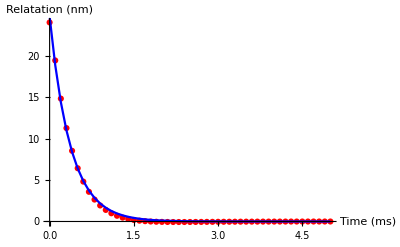

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 4.85625 | 0.0908163 | 53.4734 | 9.38463×10^-44
tau1 | 0.370121 | 1.45459×10^6 | 2.5445×10^-7 | 1.
A2 | 19.8393 | 0.0900762 | 220.25 | 1.70284×10^-72
tau2 | 0.370121 | 356055. | 1.03951×10^-6 | 0.999999

AdjustedRSquared | 0.998578
AIC | -12.4444
BIC | -2.78528
RSquared | 0.99869

```mathematica
Yfittable = Table[{t,Y6f[t+t6peak]-Y[6,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[6]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.403118 | 0.00299673 | 134.519 | 1.33596×10^-64
A | 27.038 | 0.126176 | 214.288 | 1.71568×10^-74

AdjustedRSquared | 0.99931
AIC | -38.7926
BIC | -32.9971
RSquared | 0.999337

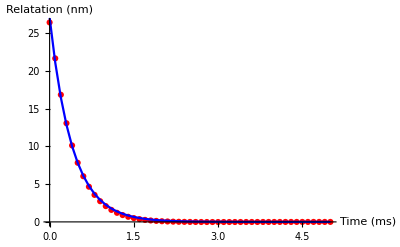

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 18.4304 | 0.0714963 | 257.781 | 1.05203×10^-75
tau1 | 0.403118 | 516168. | 7.80983×10^-7 | 0.999999
A2 | 8.60764 | 0.0714114 | 120.536 | 3.25927×10^-60
tau2 | 0.403118 | 1.1052×10^6 | 3.64747×10^-7 | 1.

AdjustedRSquared | 0.999281
AIC | -34.6673
BIC | -25.0081
RSquared | 0.999337

```mathematica
Yfittable = Table[{t,Y5f[t+t5peak]-Y[5,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[5]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.446751 | 0.00228354 | 195.639 | 1.47814×10^-72
A | 29.8966 | 0.0970107 | 308.179 | 3.21891×10^-82

AdjustedRSquared | 0.999672
AIC | -62.4509
BIC | -56.6555
RSquared | 0.999685

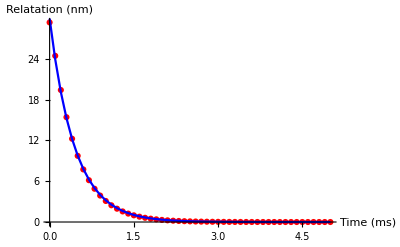

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 11.3514 | 0.0553191 | 205.199 | 4.72603×10^-71
tau1 | 0.446751 | 438406. | 1.01903×10^-6 | 0.999999
A2 | 18.5452 | 0.0553904 | 334.809 | 4.87766×10^-81
tau2 | 0.446751 | 268346. | 1.66483×10^-6 | 0.999999

AdjustedRSquared | 0.999659
AIC | -58.3256
BIC | -48.6665
RSquared | 0.999685

```mathematica
Yfittable = Table[{t,Y4f[t+t4peak]-Y[4,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[4]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.496798 | 0.00197551 | 251.478 | 6.78973×10^-78
A | 32.0922 | 0.0818683 | 391.998 | 2.45592×10^-87

AdjustedRSquared | 0.999801
AIC | -76.324
BIC | -70.5285
RSquared | 0.999809

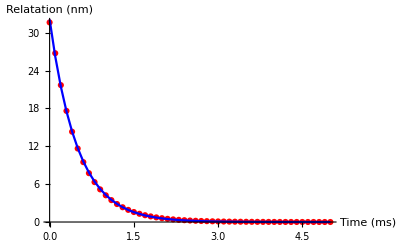

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 20.0693 | 0.0466271 | 430.42 | 3.65081×10^-86
tau1 | 0.496798 | 453685. | 1.09503×10^-6 | 0.999999
A2 | 12.0229 | 0.0475144 | 253.038 | 2.51679×10^-75
tau2 | 0.496798 | 757313. | 6.56001×10^-7 | 0.999999

AdjustedRSquared | 0.999793
AIC | -72.1987
BIC | -62.5396
RSquared | 0.999809

```mathematica
Yfittable = Table[{t,Y3f[t+t3peak]-Y[3,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[3]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.550522 | 0.00196992 | 279.464 | 3.87159×10^-80
A | 31.2761 | 0.0724609 | 431.627 | 2.19466×10^-89

AdjustedRSquared | 0.999839
AIC | -85.2881
BIC | -79.4926
RSquared | 0.999845

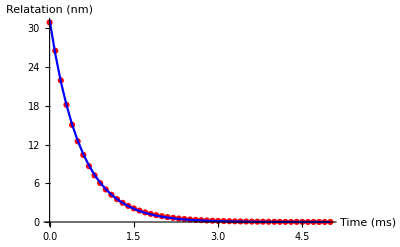

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 31.1103 | 0.414422 | 75.0691 | 1.34328×10^-50
tau1 | 0.544227 | 0.00718787 | 75.7146 | 9.01176×10^-51
A2 | 0.213512 | 0.43598 | 0.489729 | 0.626604
tau2 | 1.98604 | 2.5007 | 0.794194 | 0.431074

AdjustedRSquared | 0.999847
AIC | -86.1794
BIC | -76.5202
RSquared | 0.999859

```mathematica
Yfittable = Table[{t,Y2f[t+t2peak]-Y[2,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[2]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.60678 | 0.00203442 | 298.257 | 1.59874×10^-81
A | 23.0333 | 0.0504004 | 457.006 | 1.33596×10^-90

AdjustedRSquared | 0.999858
AIC | -118.878
BIC | -113.082
RSquared | 0.999864

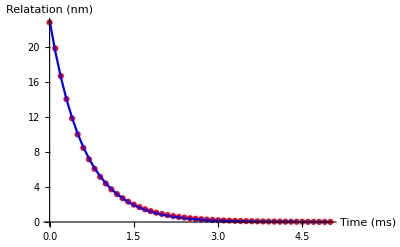

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 0.424729 | 0.683532 | 0.621374 | 0.537356
tau1 | 1.53201 | 1.08244 | 1.41533 | 0.163564
A2 | 22.6673 | 0.665236 | 34.074 | 8.65444×10^-35
tau2 | 0.593344 | 0.0111772 | 53.085 | 1.3147×10^-43

AdjustedRSquared | 0.999882
AIC | -126.225
BIC | -116.566
RSquared | 0.999891

```mathematica
Yfittable = Table[{t,Y1f[t+t1peak]-Y[1,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
taufit[[1]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

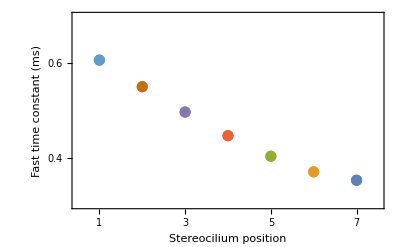

```mathematica
(*Stereocilium farthest from probe relaxes with the smallest time constant!*)
(*Chose gammaL/KL to match experimental time constants*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = 7;
Ymin=0;
Ymax =1;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-1}];
ListPlot[Reverse[Table[{{n,taufit[[n]]}},{n,1,ntotv-1}]],PlotRange->{{Xmin-0.5,Xmax+0.5},{0.3,0.7}},PlotStyle->Table[{ColorData[97,"ColorList"][[m]],PointSize[0.02]},{m,1,ntotv-1}],IntervalMarkersStyle->Table[{ColorData[97,"ColorList"][[m]],PointSize[0.02]},{m,1,ntotv-1}],Frame->{{True,False},{True,False}},FrameLabel->{"Stereocilium position","Fast time constant (ms)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(***********************************)
(***********************************)
```

```mathematica
(*Speed up stimulus to approximate ideal step*)
ntotv = ssnstereoList[[wingindexnum2]]
Y0v = 250 (*nm*);
slopefac = 10^9;
ts = 5;
te = 55;
trange = 60;
Y0slowf[t_] := Y0v*Evaluate[(1+Exp[-(t-ts)*slopefac])^-1-(1+Exp[-(t-te)*slopefac])^-1];
```

8

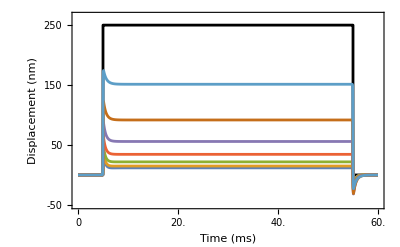

```mathematica
(*Stimulus and responses*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=-50;
Ymax =250;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
FastPlot=Show[Plot[{Y0f[t]},{t,0,trange},PlotRange->{-50,Ymax+15},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

```mathematica
(***********************************)
(***********************************)
```

```mathematica
(*Slow stimulus to remove reverse*)
ntotv = ssnstereoList[[wingindexnum2]]
Y0v = 250 (*nm*);
slopefac = 1;
ts = 5;
te = 55;
trange = 60;
Y0slowf[t_] := Y0v*Evaluate[(1+Exp[-(t-ts)*slopefac])^-1-(1+Exp[-(t-te)*slopefac])^-1];
```

8

0.8

0.670773

{{Y1→InterpolatingFunction[…],Y2→InterpolatingFunction[…],Y3→InterpolatingFunction[…],Y4→InterpolatingFunction[…],Y5→InterpolatingFunction[…],Y6→InterpolatingFunction[…],Y7→InterpolatingFunction[…]}}

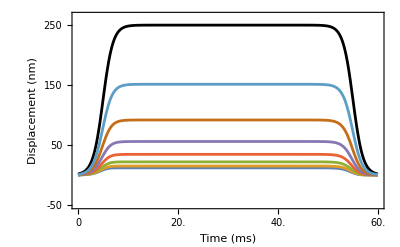

```mathematica
(*Doesn't work unless we use the equation simplification method*)
(*8 cilia, Y0 clamped, all cilia have rootlets. For 10 kHz low-pass filtered experimental stimulus use s = 10*4 = 40 such that the maximum slope is 5 kHz.*)
KLv = 5;(*mN/m*)
KAv = ssAoLList[[wingindexnum2,1,2]]*KLv;
gammaLv = 0.8*KLv;(*uN.s/m*)
gammaLv/KLv(*ms*)
gammaAv = onsetAoLList[[wingindexnum2,1,2]]*gammaLv;
KAoLv = KAv/KLv;
gammaAoLv = gammaAv/gammaLv;
(*Geometric mean time constant*)
taugmv =(gammaLv/KLv)*(g[ntotv-1,gammaAoLv,1]/g[ntotv-1,KAv/KLv,1])^(1/(ntotv-1))
KA1v = KAv;gammaA1v =gammaAv;
KA2v = KAv;gammaA2v =gammaAv;
KA3v = KAv;gammaA3v =gammaAv;
KA4v = KAv;gammaA4v =gammaAv;
KA5v = KAv;gammaA5v =gammaAv;
KA6v = KAv;gammaA6v =gammaAv;
KA7v = KAv;gammaA7v =gammaAv;
K1v = KLv;gamma1v = gammaLv;
K2v = KLv;gamma2v = gammaLv;
K3v = KLv;gamma3v = gammaLv;
K4v = KLv;gamma4v = gammaLv;
K5v = KLv;gamma5v = gammaLv;
K6v = KLv;gamma6v = gammaLv;
K7v = KLv;gamma7v = gammaLv;
Ysln=NDSolve[{KA1v*Y1[t]+gammaA1v*Y1'[t]+K1v*(Y1[t]-Y0f[t])-K2v*(Y2[t]-Y1[t])+gamma1v*(Y1'[t]-Y0f'[t])-gamma2v*(Y2'[t]-Y1'[t])==0,Y1[0]==0,KA2v*Y2[t]+gammaA2v*Y2'[t]+K2v*(Y2[t]-Y1[t])-K3v*(Y3[t]-Y2[t])+gamma2v*(Y2'[t]-Y1'[t])-gamma3v*(Y3'[t]-Y2'[t])==0,Y2[0]==0,KA3v*Y3[t]+gammaA3v*Y3'[t]+K3v*(Y3[t]-Y2[t])-K4v*(Y4[t]-Y3[t])+gamma3v*(Y3'[t]-Y2'[t])-gamma4v*(Y4'[t]-Y3'[t])==0,Y3[0]==0,KA4v*Y4[t]+gammaA4v*Y4'[t]+K4v*(Y4[t]-Y3[t])-K5v*(Y5[t]-Y4[t])+gamma4v*(Y4'[t]-Y3'[t])-gamma5v*(Y5'[t]-Y4'[t])==0,Y4[0]==0,KA5v*Y5[t]+gammaA5v*Y5'[t]+K5v*(Y5[t]-Y4[t])-K6v*(Y6[t]-Y5[t])+gamma5v*(Y5'[t]-Y4'[t])-gamma6v*(Y6'[t]-Y5'[t])==0,Y5[0]==0,KA6v*Y6[t]+gammaA6v*Y6'[t]+K6v*(Y6[t]-Y5[t])-K7v*(Y7[t]-Y6[t])+gamma6v*(Y6'[t]-Y5'[t])-gamma7v*(Y7'[t]-Y6'[t])==0,Y6[0]==0,KA7v*Y7[t]+gammaA7v*Y7'[t]+K7v*(Y7[t]-Y6[t])+gamma7v*(Y7'[t]-Y6'[t])==0,Y7[0]==0},{Y1,Y2,Y3,Y4,Y5,Y6,Y7},{t,0,trange},Method->{"EquationSimplification"->"Residual"}]
Y1slowf[t_]:=Evaluate[Y1[t]/.Ysln[[1]]]
Y2slowf[t_]:=Evaluate[Y2[t]/.Ysln[[1]]]
Y3slowf[t_]:=Evaluate[Y3[t]/.Ysln[[1]]]
Y4slowf[t_]:=Evaluate[Y4[t]/.Ysln[[1]]]
Y5slowf[t_]:=Evaluate[Y5[t]/.Ysln[[1]]]
Y6slowf[t_]:=Evaluate[Y6[t]/.Ysln[[1]]]
Y7slowf[t_]:=Evaluate[Y7[t]/.Ysln[[1]]]
(*Stimulus and responses*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=-50;
Ymax =250;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
SlowPlot=Show[Plot[{Y0slowf[t]},{t,0,trange},PlotRange->{-50,Ymax+15},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7slowf[t],Y6slowf[t],Y5slowf[t],Y4slowf[t],Y3slowf[t],Y2slowf[t],Y1slowf[t]},{t,0,trange},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

```mathematica
(***********************************)
(***********************************)
```

```mathematica
(*Slow offset speed in comparison to onset speed*)
```

```mathematica
(*Match slope of stimulus to experimental data*)
ntotv = ssnstereoList[[wingindexnum2]]
Y0v = 250 (*nm*);
slopefaconset = 50;
slopefacoffset = 10;
ts = 5;
te = 55;
trange = 60;
Y0f[t_] := Y0v*Evaluate[(1+Exp[-(t-ts)*slopefaconset])^-1-(1+Exp[-(t-te)*slopefacoffset])^-1];
```

8

0.8

0.670773

{{Y1→InterpolatingFunction[…],Y2→InterpolatingFunction[…],Y3→InterpolatingFunction[…],Y4→InterpolatingFunction[…],Y5→InterpolatingFunction[…],Y6→InterpolatingFunction[…],Y7→InterpolatingFunction[…]}}

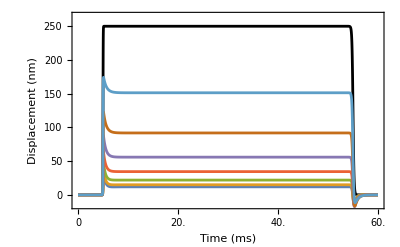

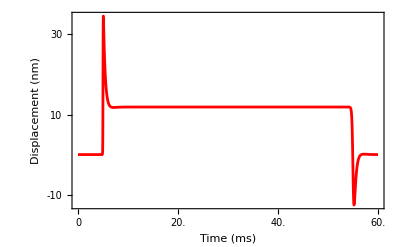

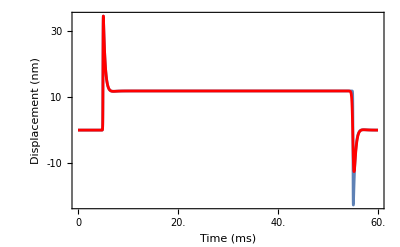

```mathematica
(*Doesn't work unless we use the equation simplification method*)
(*8 cilia, Y0 clamped, all cilia have rootlets. For 10 kHz low-pass filtered experimental stimulus use s = 10*4 = 40 such that the maximum slope is 5 kHz.*)
KLv = 5;(*mN/m*)
KAv = ssAoLList[[wingindexnum2,1,2]]*KLv;
gammaLv = 0.8*KLv;(*uN.s/m*)
gammaLv/KLv(*ms*)
gammaAv = onsetAoLList[[wingindexnum2,1,2]]*gammaLv;
KAoLv = KAv/KLv;
gammaAoLv = gammaAv/gammaLv;
(*Geometric mean time constant*)
taugmv =(gammaLv/KLv)*(g[ntotv-1,gammaAoLv,1]/g[ntotv-1,KAv/KLv,1])^(1/(ntotv-1))
KA1v = KAv;gammaA1v =gammaAv;
KA2v = KAv;gammaA2v =gammaAv;
KA3v = KAv;gammaA3v =gammaAv;
KA4v = KAv;gammaA4v =gammaAv;
KA5v = KAv;gammaA5v =gammaAv;
KA6v = KAv;gammaA6v =gammaAv;
KA7v = KAv;gammaA7v =gammaAv;
K1v = KLv;gamma1v = gammaLv;
K2v = KLv;gamma2v = gammaLv;
K3v = KLv;gamma3v = gammaLv;
K4v = KLv;gamma4v = gammaLv;
K5v = KLv;gamma5v = gammaLv;
K6v = KLv;gamma6v = gammaLv;
K7v = KLv;gamma7v = gammaLv;
Ysln=NDSolve[{KA1v*Y1[t]+gammaA1v*Y1'[t]+K1v*(Y1[t]-Y0f[t])-K2v*(Y2[t]-Y1[t])+gamma1v*(Y1'[t]-Y0f'[t])-gamma2v*(Y2'[t]-Y1'[t])==0,Y1[0]==0,KA2v*Y2[t]+gammaA2v*Y2'[t]+K2v*(Y2[t]-Y1[t])-K3v*(Y3[t]-Y2[t])+gamma2v*(Y2'[t]-Y1'[t])-gamma3v*(Y3'[t]-Y2'[t])==0,Y2[0]==0,KA3v*Y3[t]+gammaA3v*Y3'[t]+K3v*(Y3[t]-Y2[t])-K4v*(Y4[t]-Y3[t])+gamma3v*(Y3'[t]-Y2'[t])-gamma4v*(Y4'[t]-Y3'[t])==0,Y3[0]==0,KA4v*Y4[t]+gammaA4v*Y4'[t]+K4v*(Y4[t]-Y3[t])-K5v*(Y5[t]-Y4[t])+gamma4v*(Y4'[t]-Y3'[t])-gamma5v*(Y5'[t]-Y4'[t])==0,Y4[0]==0,KA5v*Y5[t]+gammaA5v*Y5'[t]+K5v*(Y5[t]-Y4[t])-K6v*(Y6[t]-Y5[t])+gamma5v*(Y5'[t]-Y4'[t])-gamma6v*(Y6'[t]-Y5'[t])==0,Y5[0]==0,KA6v*Y6[t]+gammaA6v*Y6'[t]+K6v*(Y6[t]-Y5[t])-K7v*(Y7[t]-Y6[t])+gamma6v*(Y6'[t]-Y5'[t])-gamma7v*(Y7'[t]-Y6'[t])==0,Y6[0]==0,KA7v*Y7[t]+gammaA7v*Y7'[t]+K7v*(Y7[t]-Y6[t])+gamma7v*(Y7'[t]-Y6'[t])==0,Y7[0]==0},{Y1,Y2,Y3,Y4,Y5,Y6,Y7},{t,0,trange},Method->{"EquationSimplification"->"Residual"}]
Y1f[t_]:=Evaluate[Y1[t]/.Ysln[[1]]]
Y2f[t_]:=Evaluate[Y2[t]/.Ysln[[1]]]
Y3f[t_]:=Evaluate[Y3[t]/.Ysln[[1]]]
Y4f[t_]:=Evaluate[Y4[t]/.Ysln[[1]]]
Y5f[t_]:=Evaluate[Y5[t]/.Ysln[[1]]]
Y6f[t_]:=Evaluate[Y6[t]/.Ysln[[1]]]
Y7f[t_]:=Evaluate[Y7[t]/.Ysln[[1]]]
(*Stimulus and responses*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=0;
Ymax =250;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
Show[Plot[{Y0f[t]},{t,0,trange},PlotRange->{Ymin-15,Ymax+15},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
(*Decay rates are different.*)
Y1peak=Evaluate[NMaximize[{Y1f[t],t<trange/2,t>0},t][[1]]];
t1peak=Evaluate[t/.NMaximize[{Y1f[t],t<trange/2,t>0},t][[2]]];
Y2peak=Evaluate[NMaximize[{Y2f[t],t<trange/2,t>0},t][[1]]];
t2peak=Evaluate[t/.NMaximize[{Y2f[t],t<trange/2,t>0},t][[2]]];
Y3peak=Evaluate[NMaximize[{Y3f[t],t<trange/2,t>0},t][[1]]];
t3peak=Evaluate[t/.NMaximize[{Y3f[t],t<trange/2,t>0},t][[2]]];
Y4peak=Evaluate[NMaximize[{Y4f[t],t<trange/2,t>0},t][[1]]];
t4peak=Evaluate[t/.NMaximize[{Y4f[t],t<trange/2,t>0},t][[2]]];
Y5peak=Evaluate[NMaximize[{Y5f[t],t<trange/2,t>0},t][[1]]];
t5peak=Evaluate[t/.NMaximize[{Y5f[t],t<trange/2,t>0},t][[2]]];
Y6peak=Evaluate[NMaximize[{Y6f[t],t<trange/2,t>0},t][[1]]];
t6peak=Evaluate[t/.NMaximize[{Y6f[t],t<trange/2,t>0},t][[2]]];
Y7peak=Evaluate[NMaximize[{Y7f[t],t<trange/2,t>0},t][[1]]];
t7peak=Evaluate[t/.NMaximize[{Y7f[t],t<trange/2,t>0},t][[2]]];
(*Stereocilium 7 response*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=-50;
Ymax =50;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,1*10^1}];
stereocilium1asymmplot=Show[Plot[{Y7f[t]},{t,0,trange},PlotRange->All,MaxRecursion-> 15,PlotStyle->{Thickness[Linewidth],Red},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
Show[stereocilium1symmplot,stereocilium1asymmplot]
```

```mathematica
(****************************)
(***********Predictions*****************)
(****************************)
```

```mathematica
Data[[wingindex[[wingindexnum2]],1]]
```

S8811019_1_left

```mathematica
Min[onsetAoLListrenum[[All,1,2]]]
Min[ssAoLListrenum[[All,1,2]]]
```

0.110505

0.154369

```mathematica
Max[onsetAoLListrenum[[All,1,2]]]
Max[ssAoLListrenum[[All,1,2]]]
```

0.391498

0.531762

```mathematica
Min[Table[ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]],{n,1,Length[ssAoLListrenum]}]]
Max[Table[ssAoLListrenum[[n,1,2]]/onsetAoLListrenum[[n,1,2]],{n,1,Length[ssAoLListrenum]}]]
```

0.860208

2.49625

```mathematica
(*Displacement stimulus*)
```

```mathematica
harmsln=Solve[{KA1v*Y1+gammaA1v*I*w*Y1+K1v*(Y1-Y0)-K2v*(Y2-Y1)+gamma1v*(I*w*Y1-I*w*Y0)-gamma2v*(I*w*Y2-I*w*Y1)==0,KA2v*Y2+gammaA2v*I*w*Y2+K2v*(Y2-Y1)-K3v*(Y3-Y2)+gamma2v*(I*w*Y2-I*w*Y1)-gamma3v*(I*w*Y3-I*w*Y2)==0,KA3v*Y3+gammaA3v*I*w*Y3+K3v*(Y3-Y2)-K4v*(Y4-Y3)+gamma3v*(I*w*Y3-I*w*Y2)-gamma4v*(I*w*Y4-I*w*Y3)==0,KA4v*Y4+gammaA4v*I*w*Y4+K4v*(Y4-Y3)-K5v*(Y5-Y4)+gamma4v*(I*w*Y4-I*w*Y3)-gamma5v*(I*w*Y5-I*w*Y4)==0,KA5v*Y5+gammaA5v*I*w*Y5+K5v*(Y5-Y4)-K6v*(Y6-Y5)+gamma5v*(I*w*Y5-I*w*Y4)-gamma6v*(I*w*Y6-I*w*Y5)==0,KA6v*Y6+gammaA6v*I*w*Y6+K6v*(Y6-Y5)-K7v*(Y7-Y6)+gamma6v*(I*w*Y6-I*w*Y5)-gamma7v*(I*w*Y7-I*w*Y6)==0,KA7v*Y7+gammaA6v*I*w*Y7+K7v*(Y7-Y6)+gamma7v*(I*w*Y7-I*w*Y6)==0},{Y1,Y2,Y3,Y4,Y5,Y6,Y7}];
```

```mathematica
Y1harmf[w_,Y0_]:=Evaluate[Y1/.harmsln[[1]]]
Y2harmf[w_,Y0_]:=Evaluate[Y2/.harmsln[[1]]]
Y3harmf[w_,Y0_]:=Evaluate[Y3/.harmsln[[1]]]
Y4harmf[w_,Y0_]:=Evaluate[Y4/.harmsln[[1]]]
Y5harmf[w_,Y0_]:=Evaluate[Y5/.harmsln[[1]]]
Y6harmf[w_,Y0_]:=Evaluate[Y6/.harmsln[[1]]]
Y7harmf[w_,Y0_]:=Evaluate[Y7/.harmsln[[1]]]
```

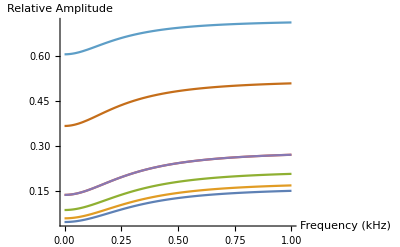

```mathematica
Plot[{Abs[Y7harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y6harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y5harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y4harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y4harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y2harmf[2*Pi*f,Y0v]]/Y0v,Abs[Y1harmf[2*Pi*f,Y0v]]/Y0v},{f,0,1},PlotRange->{0,All},AxesLabel->{"Frequency (kHz)","Relative Amplitude"},AxesStyle->Directive[Black,FontSize->12]]
```

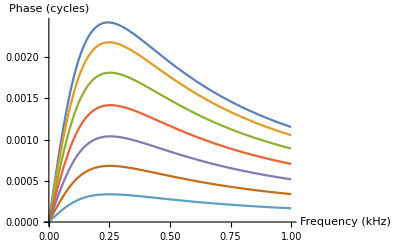

```mathematica
Plot[{Arg[Y7harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y6harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y5harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y4harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y3harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y2harmf[2*Pi*f,Y0v]]/Y0v,Arg[Y1harmf[2*Pi*f,Y0v]]/Y0v},{f,0,1},PlotRange->{0,All},AxesLabel->{"Frequency (kHz)","Phase (cycles)"},AxesStyle->Directive[Black,FontSize->12]]
```

```mathematica
KAv/KLv
gammaAv/gammaLv
(KAv/KLv)/(gammaAv/gammaLv)
```

0.258281

0.113523

2.27514

```mathematica
(*Low frequency determined by KAv/KLv and high frequency determined by gammaAv/gammaLv*)
(*Ratio of Y7 to input Y0*)
YPW[KAv/KLv,8,ntotv,Y0v]/Y0v
Abs[Y7harmf[2*Pi*0,Y0v]]/Y0v
YPW[gammaAv/gammaLv,8,ntotv,Y0v]/Y0v
Abs[Y7harmf[2*Pi*1000,Y0v]]/Y0v
```

0.047462

0.047462

0.162909

0.162909

```mathematica
(*Maximum 1/AoL across all stereocilia*)
1/Min[Table[onsetAoLListrenum[[n,1,2]],{n,1,Length[ssAoLListrenum]}]]
1/Min[Table[ssAoLListrenum[[n,1,2]],{n,1,Length[ssAoLListrenum]}]]
```

9.04939

6.478

```mathematica
(*Use wingindexrenum = 31 for wingindexnum2 = 37*)
```

```mathematica
wingindexrenum2 = 31;
```

```mathematica
(*Relative displacements within example wing*)
Table[YPW[onsetAoLListrenum[[wingindexrenum2,1,2]],m,ssnstereoListrenum[[wingindexrenum2]],1],{m,2,ssnstereoListrenum[[wingindexrenum2]]}]
```

{0.71952,0.520721,0.381037,0.284609,0.220491,0.181403,0.162909}

```mathematica
(*Relative displacements for all wings*)
relonset=Table[Table[YPW[onsetAoLListrenum[[n,1,2]],m,onsetnstereoListrenum[[n]],1],{m,2,ssnstereoListrenum[[n]]}],{n,1,Length[ssAoLListrenum]}];
relss=Table[Table[YPW[ssAoLListrenum[[n,1,2]],m,ssnstereoListrenum[[n]],1],{m,2,ssnstereoListrenum[[n]]}],{n,1,Length[ssAoLListrenum]}];
```

```mathematica
Max[relonset]
Min[relonset]
Max[relss]
Min[relss]
Mean[Flatten[{Flatten[relonset],Flatten[relss]}]]
```

0.72069

0.0111593

0.677825

0.00492661

0.236265

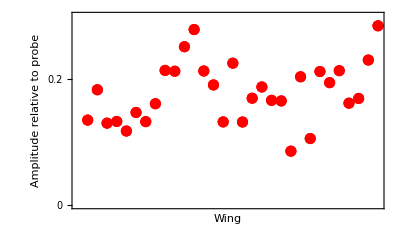

```mathematica
(*Stereocilium 5's high-frequency amplitude relative to probe*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = 31;
Ymin=0;
Ymax =1;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-1}];
ListPlot[Table[{{n,YPW[onsetAoLListrenum[[n,1,2]],5,onsetnstereoListrenum[[n]],1]}},{n,1,Length[onsetAoLListrenum]}],PlotRange->{Ymin,0.3},PlotStyle->{{Red,Thickness[Linewidth],PointSize[0.02]}},Frame->{{True,False},{True,False}},FrameTicks->{None,YTicks},FrameLabel->{"Wing","Amplitude relative to probe"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

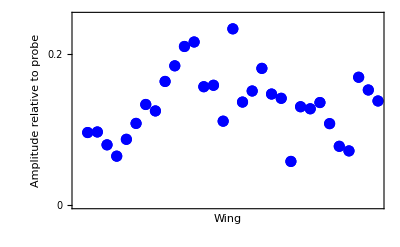

```mathematica
(*Stereocilium 5's low-frequency amplitude relative to probe*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = 31;
Ymin=0;
Ymax =1;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-1}];
ListPlot[Table[{{n,YPW[ssAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]}},{n,1,Length[ssAoLListrenum]}],PlotRange->{Ymin,0.25},PlotStyle->{{Blue,Thickness[Linewidth],PointSize[0.02]}},Frame->{{True,False},{True,False}},FrameTicks->{None,YTicks},FrameLabel->{"Wing","Amplitude relative to probe"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(*Range of high to low frequency ratios for the example wing*)
Max[Table[YPW[onsetAoLListrenum[[wingindexrenum2,1,2]],m,ssnstereoListrenum[[wingindexrenum2]],1]/YPW[ssAoLListrenum[[wingindexrenum2,1,2]],m,ssnstereoListrenum[[wingindexrenum2]],1],{m,2,ssnstereoListrenum[[wingindexrenum2]]}]]
Min[Table[YPW[onsetAoLListrenum[[wingindexrenum2,1,2]],m,ssnstereoListrenum[[wingindexrenum2]],1]/YPW[ssAoLListrenum[[wingindexrenum2,1,2]],m,ssnstereoListrenum[[wingindexrenum2]],1],{m,2,ssnstereoListrenum[[wingindexrenum2]]}]]
```

3.43242

1.18864

```mathematica
(*Number and fraction of stereocilia in 31 wings with high_freq > fac*low_freq*)
fac = 2;
wingsize = Max[ssnstereoListrenum];
Sum[Count[Table[If[ssnstereoListrenum[[n]]≥m,YPW[onsetAoLListrenum[[n,1,2]],m,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],m,ssnstereoListrenum[[n]],1]>fac,0],{m,2,wingsize}],True],{n,1,Length[ssAoLListrenum]}]
N[Sum[Count[Table[If[ssnstereoListrenum[[n]]≥m,YPW[onsetAoLListrenum[[n,1,2]],m,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],m,ssnstereoListrenum[[n]],1]>fac,0],{n,1,Length[ssAoLListrenum]}],True],{m,2,wingsize}]/Sum[Count[Table[If[ssnstereoListrenum[[n]]≥m,True,0],{m,2,wingsize}],True],{n,1,Length[ssAoLListrenum]}]]
```

26

0.124402

2.74821

0.828776

4

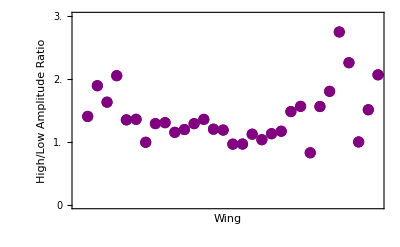

```mathematica
(*Stereocilium 5*)
(*Max and min (high freq)/(low freq) ratio*)
fac = 2;
Max[Table[YPW[onsetAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1],{n,1,Length[ssAoLListrenum]}]]
Min[Table[YPW[onsetAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1],{n,1,Length[ssAoLListrenum]}]]
(*Number of stereocilia with a high/low > fac*)
Count[Table[YPW[onsetAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]>fac,{n,1,Length[ssAoLListrenum]}],True]
(*Stereocilium 5's ratio of high frequency to low frequency amplitudes*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = 31;
Ymin=0;
Ymax =3;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,5*10^-1}];
ListPlot[Table[{{n,YPW[onsetAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]/YPW[ssAoLListrenum[[n,1,2]],5,ssnstereoListrenum[[n]],1]}},{n,1,Length[ssAoLListrenum]}],PlotRange->{Ymin,Ymax},PlotStyle->{{Purple,Thickness[Linewidth],PointSize[0.02]}},Frame->{{True,False},{True,False}},FrameTicks->{None,YTicks},FrameLabel->{"Wing","High/Low Amplitude Ratio"},Joined->False,FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

```mathematica
(*Ampl relative to displaced probe*)
YsinRelYs[ntot_,n_,KL_,KA_,gammaL_,gammaA_,w_]:=g[ntot-n-1,(KA+I*w*gammaA)/(KL+I*w*gammaL),1]/g[ntot-1,(KA+I*w*gammaA)/(KL+I*w*gammaL),1]
```

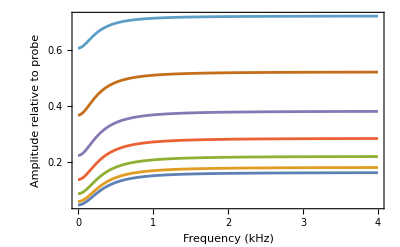

```mathematica
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = 4;
Ymin=0;
Ymax =1;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-1}];
Plot[{Abs[YsinRelYs[ntotv,7,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,6,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,5,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,4,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,3,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,2,KLv,KAv,gammaLv,gammaAv,2*Pi*f]],Abs[YsinRelYs[ntotv,1,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]},{f,0,4},PlotRange->{{0,All},{0,All}},PlotStyle->{{Thickness[Linewidth]}},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Frequency (kHz)","Amplitude relative to probe"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]
```

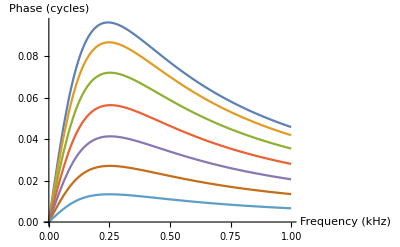

```mathematica
(*Phase rel to displaced probe*)
Plot[{Arg[YsinRelYs[ntotv,7,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,6,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,5,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,4,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,3,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,2,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi),Arg[YsinRelYs[ntotv,1,KLv,KAv,gammaLv,gammaAv,2*Pi*f]]/(2*Pi)},{f,0,1},PlotRange->{0,All},AxesLabel->{"Frequency (kHz)","Phase (cycles)"},AxesStyle->Directive[Black,FontSize->12]]
```

{{Y1→InterpolatingFunction[…],Y2→InterpolatingFunction[…],Y3→InterpolatingFunction[…],Y4→InterpolatingFunction[…],Y5→InterpolatingFunction[…],Y6→InterpolatingFunction[…],Y7→InterpolatingFunction[…]}}

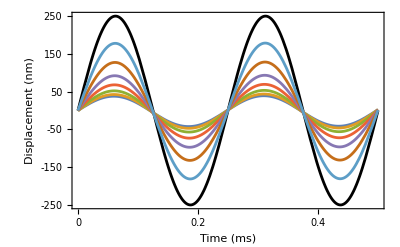

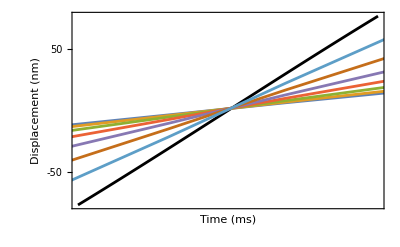

```mathematica
(*Response of representative wing to 4 kHz displacement of probe*)
fv = 4;(*kHz*)
trange = 2/fv;(*ms*)
omegav = 2*Pi*fv;
Y0f[t_] := Y0v*Evaluate[Sin[omegav*t]]
Ysln=NDSolve[{KA1v*Y1[t]+gammaA1v*Y1'[t]+K1v*(Y1[t]-Y0f[t])-K2v*(Y2[t]-Y1[t])+gamma1v*(Y1'[t]-Y0f'[t])-gamma2v*(Y2'[t]-Y1'[t])==0,Y1[0]==0,KA2v*Y2[t]+gammaA2v*Y2'[t]+K2v*(Y2[t]-Y1[t])-K3v*(Y3[t]-Y2[t])+gamma2v*(Y2'[t]-Y1'[t])-gamma3v*(Y3'[t]-Y2'[t])==0,Y2[0]==0,KA3v*Y3[t]+gammaA3v*Y3'[t]+K3v*(Y3[t]-Y2[t])-K4v*(Y4[t]-Y3[t])+gamma3v*(Y3'[t]-Y2'[t])-gamma4v*(Y4'[t]-Y3'[t])==0,Y3[0]==0,KA4v*Y4[t]+gammaA4v*Y4'[t]+K4v*(Y4[t]-Y3[t])-K5v*(Y5[t]-Y4[t])+gamma4v*(Y4'[t]-Y3'[t])-gamma5v*(Y5'[t]-Y4'[t])==0,Y4[0]==0,KA5v*Y5[t]+gammaA5v*Y5'[t]+K5v*(Y5[t]-Y4[t])-K6v*(Y6[t]-Y5[t])+gamma5v*(Y5'[t]-Y4'[t])-gamma6v*(Y6'[t]-Y5'[t])==0,Y5[0]==0,KA6v*Y6[t]+gammaA6v*Y6'[t]+K6v*(Y6[t]-Y5[t])-K7v*(Y7[t]-Y6[t])+gamma6v*(Y6'[t]-Y5'[t])-gamma7v*(Y7'[t]-Y6'[t])==0,Y6[0]==0,KA7v*Y7[t]+gammaA7v*Y7'[t]+K7v*(Y7[t]-Y6[t])+gamma7v*(Y7'[t]-Y6'[t])==0,Y7[0]==0},{Y1,Y2,Y3,Y4,Y5,Y6,Y7},{t,0,trange}]
Y1f[t_]:=Evaluate[Y1[t]/.Ysln[[1]]]
Y2f[t_]:=Evaluate[Y2[t]/.Ysln[[1]]]
Y3f[t_]:=Evaluate[Y3[t]/.Ysln[[1]]]
Y4f[t_]:=Evaluate[Y4[t]/.Ysln[[1]]]
Y5f[t_]:=Evaluate[Y5[t]/.Ysln[[1]]]
Y6f[t_]:=Evaluate[Y6[t]/.Ysln[[1]]]
Y7f[t_]:=Evaluate[Y7[t]/.Ysln[[1]]]
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=-Y0v;
Ymax =Y0v;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^-1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
(*Stimulus and responses*)
Show[Plot[{Y0f[t]},{t,0,trange},PlotStyle->{Thickness[Linewidth],Black},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->True],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
Show[Plot[{Y0f[t]},{t,0.95/fv,1.05/fv},PlotStyle->{Thickness[Linewidth],Black},Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```

```mathematica
(*Delay in ms*)
FindRoot[Y0f[t]==0,{t,0.1}]
FindRoot[Y1f[t]==0,{t,0.1}]
FindRoot[Y2f[t]==0,{t,0.1}]
FindRoot[Y3f[t]==0,{t,0.1}]
FindRoot[Y4f[t]==0,{t,0.1}]
FindRoot[Y5f[t]==0,{t,0.1}]
FindRoot[Y6f[t]==0,{t,0.1}]
FindRoot[Y7f[t]==0,{t,0.1}]
(*Maximum phase delay*)
(t/.FindRoot[Y0f[t]==0,{t,0.1}])-(t/.FindRoot[Y7f[t]==0,{t,0.1}])
```

{t→0.125}

{t→0.124202}

{t→0.123389}

{t→0.122553}

{t→0.121699}

{t→0.120863}

{t→0.120146}

{t→0.119714}

0.00528617

```mathematica
(*Frog pivots and connectors (Kozlov11 SI) in IHC bundle*)
lambdas = 0.5*10^-9;(*N.s/m, page 37*)
Lmax = 7.8*10^-6;(*m*)
Lmin=3.25*10^-6;(*m*)
lambdathetamin = lambdas*Lmin^2
lambdathetamax = lambdas*Lmax^2
LIHC = 5*10^-6;(*Nam15*)
lambdasmin = lambdathetamin/LIHC^2
lambdasmax = lambdathetamax/LIHC^2
lambdacmin = 10^3*10^-9;
lambdacmax = 10^4*10^-9;
lambdasOlambdacmax = lambdasmax/lambdacmin
lambdasOlambdacmin = lambdasmin/lambdacmax
```

5.28125×10^-21

3.042×10^-20

2.1125×10^-10

1.2168×10^-9

0.0012168

0.000021125

```mathematica
(*Frog pivots and connectors (Kozlov11 SI) in IHC bundle*)
Ks = 0.3*10^-6;(*N.s/m, page 37*)
Kthetamin = Ks*Lmin^2
Kthetamax = Ks*Lmax^2
Ksmin = Kthetamin/LIHC^2
Ksmax = Kthetamax/LIHC^2
Kc = 20*10^-3;
KsOKcmax = Ksmax/Kc
KsOKcmin = Ksmin/Kc
```

3.16875×10^-18

1.8252×10^-17

1.2675×10^-7

7.3008×10^-7

0.000036504

6.3375×10^-6

```mathematica
(*How much stronger are IHC links vs frog links?*)
{Max[onsetAoLListrenum[[All,1,2]]]/lambdasOlambdacmin,Min[onsetAoLListrenum[[All,1,2]]]/lambdasOlambdacmax}
{Max[ssAoLListrenum[[All,1,2]]]/KsOKcmin,Min[ssAoLListrenum[[All,1,2]]]/KsOKcmax}
```

{18532.4,90.8158}

{83907.2,4228.81}

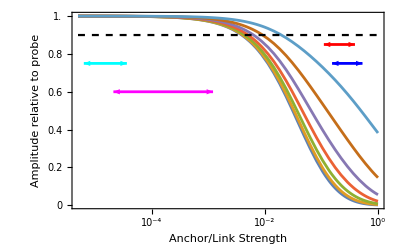

```mathematica
(*Yn relative to Y0 as a function of AoL ratio*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 10^-6;
XpowMin = MantissaExponent[Xmin][[2]]-1;
Xmax = 10^0;
XpowMax = MantissaExponent[Xmax][[2]]+1;
Ymin=0;
Ymax =1;
BottomTicks=Table[{10^i,Superscript[10,i],{0,TickLength}},{i,XpowMin,XpowMax,1}];
XminorTicks = Flatten[Table[{j*10^i,Null,{0,TickLength/2},Thickness[0.005]},{i,XpowMin,XpowMax,1},{j,1,9,1}],1];
XTicks=Table[{i,N[i,1],{0,TickLength}},{i,Xmin,Xmax,1*10^-1}];
YTicks=Table[{i,N[i,1],{0,TickLength}},{i,Ymin,Ymax,2*10^-1}];
Show[LogLinearPlot[{YPW[AoL,8,ntotv,Y0v]/Y0v,YPW[AoL,7,ntotv,Y0v]/Y0v,YPW[AoL,6,ntotv,Y0v]/Y0v,YPW[AoL,5,ntotv,Y0v]/Y0v,YPW[AoL,4,ntotv,Y0v]/Y0v,YPW[AoL,3,ntotv,Y0v]/Y0v,YPW[AoL,2,ntotv,Y0v]/Y0v},{AoL,5*Xmin,Xmax},PlotRange->All,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameLabel->{"Anchor/Link Strength","Amplitude relative to probe"},FrameTicks->{{YTicks,YTicks},{Join[BottomTicks,XminorTicks],XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],LogLinearPlot[0.9,{AoL,5*Xmin,Xmax},PlotRange->All,AxesLabel->{"Ratio","Relative Amplitude"},AxesStyle->Directive[Black,FontSize->12],PlotStyle->{Black,Dashed}],Graphics[{Thickness[Linewidth],Blue,Arrowheads[{-0.04,0.04}],Arrow[{{Log[Min[ssAoLListrenum[[All,1,2]]]],0.75},{Log[Max[ssAoLListrenum[[All,1,2]]]],0.75}}]}],Graphics[{Thickness[Linewidth],Red,Arrowheads[{-0.04,0.04}],Arrow[{{Log[Min[onsetAoLListrenum[[All,1,2]]]],0.85},{Log[Max[onsetAoLListrenum[[All,1,2]]]],0.85}}]}],Graphics[{Thickness[Linewidth],Cyan,Arrowheads[{-0.04,0.04}],Arrow[{{Log[KsOKcmin],0.75},{Log[KsOKcmax],0.75}}]}],Graphics[{Thickness[Linewidth],Magenta,Arrowheads[{-0.04,0.04}],Arrow[{{Log[lambdasOlambdacmin],0.6},{Log[lambdasOlambdacmax],0.6}}]}]]
```

```mathematica
(*****************Ideal Step************)
```

```mathematica
(*Start at begining of step. Use analytical peak solutions for stereocilia initial conditions.*)
ntotv = ssnstereoList[[wingindexnum2]]
Y0v = 250 (*nm*);
trange = 60;
Y0f[t_] := Y0v;
```

8

0.8

0.670773

{{Y1→InterpolatingFunction[…],Y2→InterpolatingFunction[…],Y3→InterpolatingFunction[…],Y4→InterpolatingFunction[…],Y5→InterpolatingFunction[…],Y6→InterpolatingFunction[…],Y7→InterpolatingFunction[…]}}

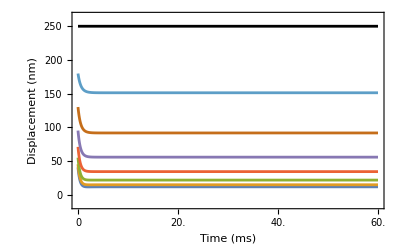

```mathematica
(*Doesn't work unless we use the equation simplification method*)
(*8 cilia, Y0 clamped, all cilia have rootlets.*)
KLv = 5;(*mN/m*)
KAv = ssAoLList[[wingindexnum2,1,2]]*KLv;
gammaLv = 0.8*KLv;(*uN.s/m*)
gammaLv/KLv(*ms*)
gammaAv = onsetAoLList[[wingindexnum2,1,2]]*gammaLv;
KAoLv = KAv/KLv;
gammaAoLv = gammaAv/gammaLv;
(*Geometric mean time constant*)
taugmv =(gammaLv/KLv)*(g[ntotv-1,gammaAoLv,1]/g[ntotv-1,KAv/KLv,1])^(1/(ntotv-1))
KA1v = KAv;gammaA1v =gammaAv;
KA2v = KAv;gammaA2v =gammaAv;
KA3v = KAv;gammaA3v =gammaAv;
KA4v = KAv;gammaA4v =gammaAv;
KA5v = KAv;gammaA5v =gammaAv;
KA6v = KAv;gammaA6v =gammaAv;
KA7v = KAv;gammaA7v =gammaAv;
K1v = KLv;gamma1v = gammaLv;
K2v = KLv;gamma2v = gammaLv;
K3v = KLv;gamma3v = gammaLv;
K4v = KLv;gamma4v = gammaLv;
K5v = KLv;gamma5v = gammaLv;
K6v = KLv;gamma6v = gammaLv;
K7v = KLv;gamma7v = gammaLv;
Ysln=NDSolve[{KA1v*Y1[t]+gammaA1v*Y1'[t]+K1v*(Y1[t]-Y0f[t])-K2v*(Y2[t]-Y1[t])+gamma1v*(Y1'[t]-Y0f'[t])-gamma2v*(Y2'[t]-Y1'[t])==0,Y1[0]==Y[1,ntotv,gammaAoLv,Y0v],KA2v*Y2[t]+gammaA2v*Y2'[t]+K2v*(Y2[t]-Y1[t])-K3v*(Y3[t]-Y2[t])+gamma2v*(Y2'[t]-Y1'[t])-gamma3v*(Y3'[t]-Y2'[t])==0,Y2[0]==Y[2,ntotv,gammaAoLv,Y0v],KA3v*Y3[t]+gammaA3v*Y3'[t]+K3v*(Y3[t]-Y2[t])-K4v*(Y4[t]-Y3[t])+gamma3v*(Y3'[t]-Y2'[t])-gamma4v*(Y4'[t]-Y3'[t])==0,Y3[0]==Y[3,ntotv,gammaAoLv,Y0v],KA4v*Y4[t]+gammaA4v*Y4'[t]+K4v*(Y4[t]-Y3[t])-K5v*(Y5[t]-Y4[t])+gamma4v*(Y4'[t]-Y3'[t])-gamma5v*(Y5'[t]-Y4'[t])==0,Y4[0]==Y[4,ntotv,gammaAoLv,Y0v],KA5v*Y5[t]+gammaA5v*Y5'[t]+K5v*(Y5[t]-Y4[t])-K6v*(Y6[t]-Y5[t])+gamma5v*(Y5'[t]-Y4'[t])-gamma6v*(Y6'[t]-Y5'[t])==0,Y5[0]==Y[5,ntotv,gammaAoLv,Y0v],KA6v*Y6[t]+gammaA6v*Y6'[t]+K6v*(Y6[t]-Y5[t])-K7v*(Y7[t]-Y6[t])+gamma6v*(Y6'[t]-Y5'[t])-gamma7v*(Y7'[t]-Y6'[t])==0,Y6[0]==Y[6,ntotv,gammaAoLv,Y0v],KA7v*Y7[t]+gammaA7v*Y7'[t]+K7v*(Y7[t]-Y6[t])+gamma7v*(Y7'[t]-Y6'[t])==0,Y7[0]==Y[7,ntotv,gammaAoLv,Y0v]},{Y1,Y2,Y3,Y4,Y5,Y6,Y7},{t,0,trange},Method->{"EquationSimplification"->"Residual"}]
Y1f[t_]:=Evaluate[Y1[t]/.Ysln[[1]]]
Y2f[t_]:=Evaluate[Y2[t]/.Ysln[[1]]]
Y3f[t_]:=Evaluate[Y3[t]/.Ysln[[1]]]
Y4f[t_]:=Evaluate[Y4[t]/.Ysln[[1]]]
Y5f[t_]:=Evaluate[Y5[t]/.Ysln[[1]]]
Y6f[t_]:=Evaluate[Y6[t]/.Ysln[[1]]]
Y7f[t_]:=Evaluate[Y7[t]/.Ysln[[1]]]
(*Stimulus and responses*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 0;
Xmax = trange;
Ymin=0;
Ymax =250;
XTicks=Table[{i,N[i,2],{0,TickLength}},{i,Xmin,Xmax,1*10^1}];
YTicks=Table[{i,i,{0,TickLength}},{i,Ymin,Ymax,5*10^1}];
Show[Plot[{Y0f[t]},{t,0,trange},PlotRange->{Ymin-15,Ymax+15},MaxRecursion-> 15,PlotStyle->{Black,Thickness[Linewidth]},Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],
Plot[{Y7f[t],Y6f[t],Y5f[t],Y4f[t],Y3f[t],Y2f[t],Y1f[t]},{t,0,trange},MaxRecursion-> 15,PlotStyle->Thickness[Linewidth],Frame->{{True,False},{True,False}},FrameTicks->{XTicks,YTicks},FrameLabel->{"Time (ms)","Displacement (nm)"},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
(*Decay rates are different.*)
Y1peak=Evaluate[NMaximize[{Y1f[t],t<trange/2,t>0},t][[1]]];
t1peak=Evaluate[t/.NMaximize[{Y1f[t],t<trange/2,t>0},t][[2]]];
Y2peak=Evaluate[NMaximize[{Y2f[t],t<trange/2,t>0},t][[1]]];
t2peak=Evaluate[t/.NMaximize[{Y2f[t],t<trange/2,t>0},t][[2]]];
Y3peak=Evaluate[NMaximize[{Y3f[t],t<trange/2,t>0},t][[1]]];
t3peak=Evaluate[t/.NMaximize[{Y3f[t],t<trange/2,t>0},t][[2]]];
Y4peak=Evaluate[NMaximize[{Y4f[t],t<trange/2,t>0},t][[1]]];
t4peak=Evaluate[t/.NMaximize[{Y4f[t],t<trange/2,t>0},t][[2]]];
Y5peak=Evaluate[NMaximize[{Y5f[t],t<trange/2,t>0},t][[1]]];
t5peak=Evaluate[t/.NMaximize[{Y5f[t],t<trange/2,t>0},t][[2]]];
Y6peak=Evaluate[NMaximize[{Y6f[t],t<trange/2,t>0},t][[1]]];
t6peak=Evaluate[t/.NMaximize[{Y6f[t],t<trange/2,t>0},t][[2]]];
Y7peak=Evaluate[NMaximize[{Y7f[t],t<trange/2,t>0},t][[1]]];
t7peak=Evaluate[t/.NMaximize[{Y7f[t],t<trange/2,t>0},t][[2]]];
```

```mathematica
(*Find effective time constants from fitting. 1 time constant is sufficient. 2 time constants doesn't work.*)
```

```mathematica
tauidealfit = Table[NaN,{n,1,ntotv-1}];
```

```mathematica
(*Time after peak to fit*)
tfitend = 5;
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.344467 | 0.00258235 | 133.393 | 2.01487×10^-64
A | 29.1737 | 0.134663 | 216.643 | 1.00474×10^-74

AdjustedRSquared | 0.999304
AIC | -36.6222
BIC | -30.8267
RSquared | 0.999331

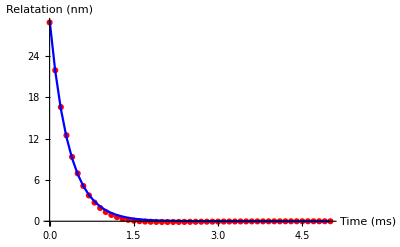

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 10.9851 | 0.0749778 | 146.512 | 3.46746×10^-64
tau1 | 0.344467 | 1.22529×10^6 | 2.81132×10^-7 | 1.
A2 | 18.1886 | 0.0757002 | 240.271 | 2.86271×10^-74
tau2 | 0.344467 | 740022. | 4.65483×10^-7 | 1.

AdjustedRSquared | 0.999274
AIC | -32.4969
BIC | -22.8378
RSquared | 0.999331

```mathematica
Yfittable = Table[{t,Y7f[t]-Y[7,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[7]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.361273 | 0.00195237 | 185.043 | 2.25489×10^-71
A | 30.6702 | 0.102685 | 298.684 | 1.49053×10^-81

AdjustedRSquared | 0.999637
AIC | -62.9686
BIC | -57.1731
RSquared | 0.999651

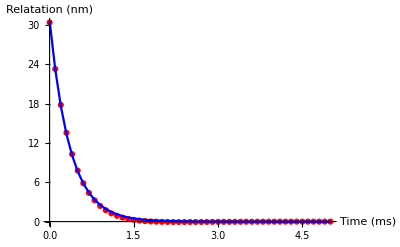

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 15.3406 | 0.0576319 | 266.182 | 2.33271×10^-76
tau1 | 0.361273 | 317449. | 1.13805×10^-6 | 0.999999
A2 | 15.3296 | 0.0576922 | 265.714 | 2.53351×10^-76
tau2 | 0.361273 | 317675. | 1.13724×10^-6 | 0.999999

AdjustedRSquared | 0.999622
AIC | -58.8433
BIC | -49.1841
RSquared | 0.999651

```mathematica
Yfittable = Table[{t,Y6f[t]-Y[6,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[6]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.39244 | 0.000952062 | 412.2 | 2.09468×10^-88
A | 33.4018 | 0.0507107 | 658.674 | 2.23041×10^-98

AdjustedRSquared | 0.999927
AIC | -132.564
BIC | -126.769
RSquared | 0.999929

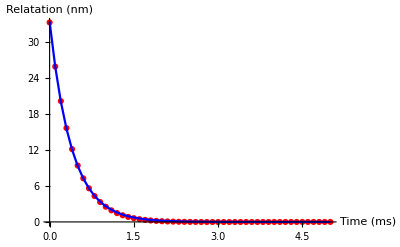

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 16.7002 | 0.027961 | 597.266 | 7.52799×10^-93
tau1 | 0.39244 | 635741. | 6.17295×10^-7 | 1.
A2 | 16.7017 | 0.0294425 | 567.263 | 8.48337×10^-92
tau2 | 0.39244 | 635684. | 6.17351×10^-7 | 1.

AdjustedRSquared | 0.999923
AIC | -128.439
BIC | -118.78
RSquared | 0.999929

```mathematica
Yfittable = Table[{t,Y5f[t]-Y[5,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[5]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.434099 | 0.000132032 | 3287.82 | 1.36737×10^-132
A | 36.7094 | 0.00706658 | 5194.8 | 2.52088×10^-142

AdjustedRSquared | 0.999999
AIC | -330.533
BIC | -324.738
RSquared | 0.999999

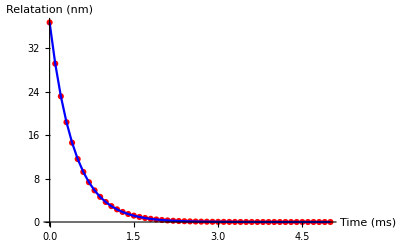

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 36.2889 | 0.122525 | 296.176 | 1.54779×10^-78
tau1 | 0.436684 | 0.00046107 | 947.109 | 2.92799×10^-102
A2 | 0.449512 | 0.121815 | 3.69013 | 0.000581485
tau2 | 0.221447 | 0.0246223 | 8.99379 | 8.74621×10^-12

AdjustedRSquared | 1.
AIC | -434.019
BIC | -424.36
RSquared | 1.

```mathematica
Yfittable = Table[{t,Y4f[t]-Y[4,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[4]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.4825 | 0.00099359 | 485.613 | 6.82415×10^-92
A | 39.2048 | 0.0516483 | 759.073 | 2.13619×10^-101

AdjustedRSquared | 0.999947
AIC | -124.274
BIC | -118.478
RSquared | 0.999949

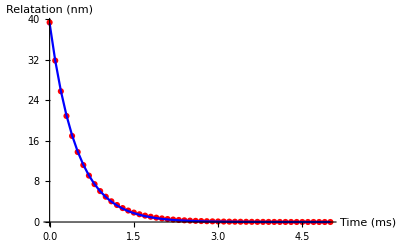

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 20.7137 | 0.16281 | 127.227 | 2.59258×10^-61
tau1 | 0.405434 | 0.000594266 | 682.242 | 1.45128×10^-95
A2 | 18.6778 | 0.163015 | 114.577 | 3.50438×10^-59
tau2 | 0.570589 | 0.000804219 | 709.494 | 2.30334×10^-96

AdjustedRSquared | 1.
AIC | -593.299
BIC | -583.639
RSquared | 1.

```mathematica
Yfittable = Table[{t,Y3f[t]-Y[3,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[3]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.535071 | 0.00163443 | 327.374 | 1.66919×10^-83
A | 38.1395 | 0.075245 | 506.87 | 8.36542×10^-93

AdjustedRSquared | 0.999882
AIC | -82.4244
BIC | -76.629
RSquared | 0.999887

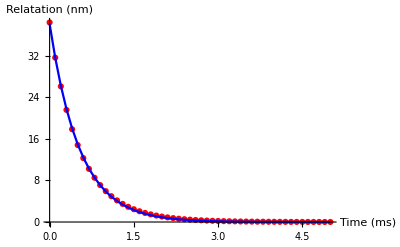

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 17.807 | 0.00920993 | 1933.46 | 7.94362×10^-117
tau1 | 0.418685 | 0.0000512111 | 8175.67 | 2.94628×10^-146
A2 | 20.6214 | 0.00923252 | 2233.56 | 9.01428×10^-120
tau2 | 0.638502 | 0.0000564517 | 11310.6 | 6.98321×10^-153

AdjustedRSquared | 1.
AIC | -818.577
BIC | -808.918
RSquared | 1.

```mathematica
Yfittable = Table[{t,Y2f[t]-Y[2,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[2]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

| Estimate | Standard Error | t-Statistic | P-Value
tau | 0.590515 | 0.00202265 | 291.95 | 4.55286×10^-81
A | 28.2872 | 0.0630983 | 448.304 | 3.4262×10^-90

AdjustedRSquared | 0.999852
AIC | -96.933
BIC | -91.1375
RSquared | 0.999858

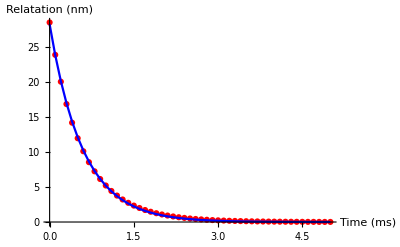

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 17.7792 | 0.0410217 | 433.409 | 2.63739×10^-86
tau1 | 0.689035 | 0.000347186 | 1984.63 | 2.32721×10^-117
A2 | 10.7672 | 0.0408811 | 263.378 | 3.83568×10^-76
tau2 | 0.431007 | 0.00043754 | 985.067 | 4.61849×10^-103

AdjustedRSquared | 1.
AIC | -631.931
BIC | -622.272
RSquared | 1.

```mathematica
Yfittable = Table[{t,Y1f[t]-Y[1,ntotv,KAoLv,Y0v]},{t,0,tfitend,0.1}];
fit=NonlinearModelFit[Yfittable,{A*Exp[-t/tau]},{tau,A},t];
Print[fit["ParameterTable"]];
Print[Grid[Transpose[{#,fit[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
tauidealfit[[1]]=Around[(tau/.fit["BestFitParameters"]),fit["ParameterTable"][[1,1,2,3]]];
Show[ListPlot[Yfittable,PlotStyle->Red,AxesLabel->{"Time (ms)","Relatation (nm)"},AxesStyle->Directive[Black,FontSize->12],PlotRange->All],ListPlot[Table[{t,(A/.fit["BestFitParameters"])*Exp[-t/(tau/.fit["BestFitParameters"])]},{t,0,tfitend,0.1}],PlotStyle->Blue,Joined->True,PlotRange->All]]
fit2=NonlinearModelFit[Yfittable,{A1*Exp[-t/tau1]+A2*Exp[-t/tau2]},{A1,tau1,A2,tau2},t];
Print[fit2["ParameterTable"]];
Print[Grid[Transpose[{#,fit2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
```

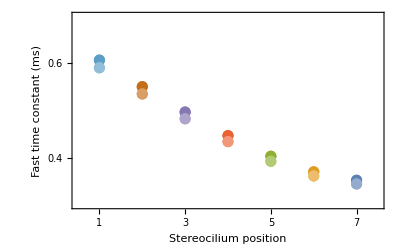

```mathematica
(*Stereocilium farthest from probe relaxes with the shortest time constant!*)
(*Choose gammaL/KL to match experimental time constants*)
(*Tick Marks*)
TickLength = 0.02;
Xmin = 1;
Xmax = 7;
Ymin=0;
Ymax =1;
XTicks=Table[{i,i,{0,TickLength}},{i,Xmin,Xmax,1}];
YTicks=Table[{i,N[i,2],{0,TickLength}},{i,Ymin,Ymax,1*10^-1}];
Show[ListPlot[Reverse[Table[{{n,taufit[[n]]}},{n,1,ntotv-1}]],PlotRange->{{Xmin-0.5,Xmax+0.5},{0.3,0.7}},PlotStyle->Table[{ColorData[97,"ColorList"][[m]],PointSize[0.02]},{m,1,ntotv-1}],IntervalMarkersStyle->Table[{ColorData[97,"ColorList"][[m]],PointSize[0.02]},{m,1,ntotv-1}],Frame->{{True,False},{True,False}},FrameLabel->{"Stereocilium position","Fast time constant (ms)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False],ListPlot[Reverse[Table[{{n,tauidealfit[[n]]}},{n,1,ntotv-1}]],PlotRange->{{Xmin-0.5,Xmax+0.5},{0.4,0.8}},PlotStyle->Table[{Lighter[ColorData[97,"ColorList"][[m]]],PointSize[0.02]},{m,1,ntotv-1}],IntervalMarkersStyle->Table[{Lighter[ColorData[97,"ColorList"][[m]]],PointSize[0.02]},{m,1,ntotv-1}],Frame->{{True,False},{True,False}},FrameLabel->{"Stereocilium position","Fast time constant (ms)"},FrameTicks->{{YTicks,YTicks},{XTicks,XTicks}},FrameStyle->{{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}},{{Black,Thickness[Linewidth],FontSize ->Fontsize},{Black,Thickness[Linewidth],FontSize ->Fontsize}}},Axes->False]]
```